```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

DropInList lässt das von einer Liste list mit inneren Listen jedes Element von from bis to fallen (jeweils inklusive)

```mathematica
DropInList[list_,from_,to_]:=Module[{buffer=list}, For[i=0,i<Length[buffer],i++;buffer[[i]]=Drop[buffer[[i]],{from,to}]];If[from⩽to,
Return[buffer],Return["It has to be from =< to"]]]
```

ErrorBarXY erzeugt eine Liste mit ErrorBar[x[[i]],y[[i]]]
Alternativ: ErrorBarXY[listXerr_,listYerr_]=ErrorBar@@@(Partition[Flatten[Riffle[listXerr,listYerr]],2])

```mathematica
ErrorBarXY[listXerr_,listYerr_]:=Module[{buffer=listXerr}, For[i=0,i<Length[buffer],i++;buffer[[i]]=ErrorBar[listXerr[[i]],listYerr[[i]]]]; If[Length[listXerr]==Length[listYerr],
Return[buffer],Return["Length of lists not equal"]]]
```

errorPlotValue erzeugt die Punkte aus listX und listY und hängt jedem Punkt die entsprechende Errorbar[listXerr,listYerr] an

```mathematica
errorPlotValue[listX_,listY_,listXerr_,listYerr_]:=Module[{buffer=listXerr,errors,points,plotValues}, errors=ErrorBarXY[listXerr,listYerr];
points=Partition[Flatten[Riffle[listX,listY]],2];
plotValues=Partition[Riffle[points,errors],2]; If[Length[listXerr]==Length[listYerr]==Length[listX]==Length[listY],
Return[plotValues],Return["Length of lists not equal"]]]
```

errorPropNew ist für die Fehlerfortpflanzung ganzer Listen geeignet. vars={{x,dx},{y,dy}...} und func eine Funktion die von x,y... abhängt. Es wird die zugehörige Fehlerfunktion zurückgegeben. Speicher diese unter einem Namen ab zB errFkt.
Nutze errFkt[f, list_x,list_dx,list_y,list_dy,...]

```mathematica
errorPropNew[func_,vars_]:=Module[{derivs=Table[0,{Length[vars]}],funcErrorForm,parameter,errFunction},

For[ii=1,ii≤Length[vars],ii++,derivs[[ii]]=D[func,vars[[ii,1]]];];
parameter=Flatten[vars];
funcErrorForm=Sqrt[Sum[(derivs[[ii]]*vars[[ii,2]])^2,{ii,Length[vars]}]];
errFunction=Function@@{parameter,funcErrorForm};
Return[errFunction];];
```

Wendet f auf die n-te Komponenten jedes Punktes in g an. Alternativ {f@First[#], Last[#]} &/@ g;

```mathematica
(*  MapAt[(f[#])&,#,n]&/@g   *)
```

## C16

M1

## I=2mA

### Messwerte

```mathematica
messwerte1=({{24.6, 30.3, 35.5, 40.0, 45.0, 50.0, 55.0, 60.0, 65.0, 70.0, 75.0, 80.0, 85.0, 90.0, 95.0, 100.0, 105.0, 110.0, 115.0, 120.0, 125.0, 130.0, 135.4, 140.0, 145.0, 150.0, 155.0, 160.0, 165.0, 170.0}, {1.693, 1.344, 1.090, 0.902, .745, .606, .503, .416, .347, .289, .241, .203, .171, .143, .121, .104, .086, .076, .065, .057, .049, .042, .036, .032, .029, .025, .022, .019, .017, .015}});
```

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
i1=2.0*10^-3;
```

```mathematica
di1=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerte1t=Transpose[messwerte1] ;
```

```mathematica
messwerte1si=MapAt[(f[#])&,#,1]&/@messwerte1t
```

{{297.75,1.693},{303.45,1.344},{308.65,1.09},{313.15,0.902},{318.15,0.745},{323.15,0.606},{328.15,0.503},{333.15,0.416},{338.15,0.347},{343.15,0.289},{348.15,0.241},{353.15,0.203},{358.15,0.171},{363.15,0.143},{368.15,0.121},{373.15,0.104},{378.15,0.086},{383.15,0.076},{388.15,0.065},{393.15,0.057},{398.15,0.049},{403.15,0.042},{408.55,0.036},{413.15,0.032},{418.15,0.029},{423.15,0.025},{428.15,0.022},{433.15,0.019},{438.15,0.017},{443.15,0.015}}

```mathematica
messwerte1si //MatrixForm
```

(297.75 | 1.693
303.45 | 1.344
308.65 | 1.09
313.15 | 0.902
318.15 | 0.745
323.15 | 0.606
328.15 | 0.503
333.15 | 0.416
338.15 | 0.347
343.15 | 0.289
348.15 | 0.241
353.15 | 0.203
358.15 | 0.171
363.15 | 0.143
368.15 | 0.121
373.15 | 0.104
378.15 | 0.086
383.15 | 0.076
388.15 | 0.065
393.15 | 0.057
398.15 | 0.049
403.15 | 0.042
408.55 | 0.036
413.15 | 0.032
418.15 | 0.029
423.15 | 0.025
428.15 | 0.022
433.15 | 0.019
438.15 | 0.017
443.15 | 0.015)

```mathematica
u1=Transpose[messwerte1si][[2]]
```

{1.693,1.344,1.09,0.902,0.745,0.606,0.503,0.416,0.347,0.289,0.241,0.203,0.171,0.143,0.121,0.104,0.086,0.076,0.065,0.057,0.049,0.042,0.036,0.032,0.029,0.025,0.022,0.019,0.017,0.015}

```mathematica
leitf[U_]:=i1/U*c/(b *d);
```

```mathematica
leitf1=leitf[#]&/@Transpose[messwerte1si][[2]]
```

{2.36267,2.97619,3.66972,4.43459,5.36913,6.60066,7.95229,9.61538,11.5274,13.8408,16.5975,19.7044,23.3918,27.972,33.0579,38.4615,46.5116,52.6316,61.5385,70.1754,81.6327,95.2381,111.111,125.,137.931,160.,181.818,210.526,235.294,266.667}

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitf1ln=g[#]&/@leitf1
```

{0.859792,1.09064,1.30012,1.48944,1.68067,1.88717,2.07346,2.26336,2.44472,2.62762,2.80925,2.98084,3.15239,3.33121,3.49826,3.64966,3.8397,3.96332,4.11966,4.251,4.40223,4.55638,4.71053,4.82831,4.92675,5.07517,5.20301,5.34961,5.46084,5.586}

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerte1xaxis=g1[#]&/@Transpose[messwerte1si][[1]]
```

{1.21628×10^20,1.19344×10^20,1.17333×10^20,1.15647×10^20,1.13829×10^20,1.12068×10^20,1.10361×10^20,1.08704×10^20,1.07097×10^20,1.05536×10^20,1.04021×10^20,1.02548×10^20,1.01116×10^20,9.97241×10^19,9.83697×10^19,9.70516×10^19,9.57684×10^19,9.45186×10^19,9.33011×10^19,9.21145×10^19,9.09577×10^19,8.98296×10^19,8.86423×10^19,8.76554×10^19,8.66072×10^19,8.55839×10^19,8.45844×10^19,8.3608×10^19,8.26539×10^19,8.17213×10^19}

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts)

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehler1u=messfehler1u[#] & /@ u1
```

{0.011465,0.00972,0.00845,0.00751,0.006725,0.00603,0.005515,0.00508,0.004735,0.004445,0.004205,0.004015,0.003855,0.003715,0.003605,0.00352,0.00343,0.00338,0.003325,0.003285,0.003245,0.00321,0.00318,0.00316,0.003145,0.003125,0.00311,0.003095,0.003085,0.003075}

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
leitf1Err=errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]@@{u1,fehler1u,i1,di1}
```

{1.18144,1.48825,1.83508,2.2176,2.685,3.30098,3.9771,4.80913,5.76583,6.92369,8.30381,9.85992,11.7078,14.0049,16.5582,19.2748,23.3297,26.4197,30.9298,35.32,41.1728,48.1722,56.4159,63.7073,70.5691,82.4621,94.4726,110.709,125.156,144.105}

```mathematica
leitf1lnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{u1,fehler1u,i1,di1}
```

{0.500046,0.500052,0.50006,0.500069,0.500081,0.500099,0.50012,0.500149,0.500186,0.500237,0.500304,0.500391,0.500508,0.500674,0.500887,0.501144,0.501588,0.501974,0.50261,0.50331,0.504367,0.505808,0.507743,0.509658,0.511626,0.515388,0.5196,0.525866,0.531913,0.540393}

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
T1GradErr=messfehler1T[#] & /@messwerte1[[1]]
```

{3.492,3.606,3.71,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.708,5.8,5.9,6.,6.1,6.2,6.3,6.4}

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}]
```

Function[{t,dt},3.62148×10^22 √(dt^2/t^4)]

```mathematica
T1K=Transpose[messwerte1si][[1]]
```

{297.75,303.45,308.65,313.15,318.15,323.15,328.15,333.15,338.15,343.15,348.15,353.15,358.15,363.15,368.15,373.15,378.15,383.15,388.15,393.15,398.15,403.15,408.55,413.15,418.15,423.15,428.15,433.15,438.15,443.15}

```mathematica
messwerte1xaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{T1K,T1GradErr}
```

{1.42645×10^18,1.4182×10^18,1.41035×10^18,1.40335×10^18,1.39536×10^18,1.3872×10^18,1.37888×10^18,1.37043×10^18,1.36187×10^18,1.35323×10^18,1.34452×10^18,1.33575×10^18,1.32695×10^18,1.31812×10^18,1.30928×10^18,1.30044×10^18,1.2916×10^18,1.28278×10^18,1.27398×10^18,1.26521×10^18,1.25648×10^18,1.24779×10^18,1.23845×10^18,1.23055×10^18,1.22201×10^18,1.21353×10^18,1.2051×10^18,1.19674×10^18,1.18845×10^18,1.18022×10^18}

### Plotten (Vorbereitung)

```mathematica
points1=Partition[Flatten[Riffle[messwerte1xaxis,leitf1ln]],2];
```

```mathematica
Length[messwerte1xaxis]
```

30

```mathematica
errors1=Table[ErrorBar[messwerte1xaxisErr[[i ]],leitf1lnErr[[i]]],{i,1,30}]
```

{ErrorBar[1.42645×10^18,0.500046],ErrorBar[1.4182×10^18,0.500052],ErrorBar[1.41035×10^18,0.50006],ErrorBar[1.40335×10^18,0.500069],ErrorBar[1.39536×10^18,0.500081],ErrorBar[1.3872×10^18,0.500099],ErrorBar[1.37888×10^18,0.50012],ErrorBar[1.37043×10^18,0.500149],ErrorBar[1.36187×10^18,0.500186],ErrorBar[1.35323×10^18,0.500237],ErrorBar[1.34452×10^18,0.500304],ErrorBar[1.33575×10^18,0.500391],ErrorBar[1.32695×10^18,0.500508],ErrorBar[1.31812×10^18,0.500674],ErrorBar[1.30928×10^18,0.500887],ErrorBar[1.30044×10^18,0.501144],ErrorBar[1.2916×10^18,0.501588],ErrorBar[1.28278×10^18,0.501974],ErrorBar[1.27398×10^18,0.50261],ErrorBar[1.26521×10^18,0.50331],ErrorBar[1.25648×10^18,0.504367],ErrorBar[1.24779×10^18,0.505808],ErrorBar[1.23845×10^18,0.507743],ErrorBar[1.23055×10^18,0.509658],ErrorBar[1.22201×10^18,0.511626],ErrorBar[1.21353×10^18,0.515388],ErrorBar[1.2051×10^18,0.5196],ErrorBar[1.19674×10^18,0.525866],ErrorBar[1.18845×10^18,0.531913],ErrorBar[1.18022×10^18,0.540393]}

```mathematica
plotValues1=Partition[Riffle[points1,errors1],2]
```

{{{1.21628×10^20,0.859792},ErrorBar[1.42645×10^18,0.500046]},{{1.19344×10^20,1.09064},ErrorBar[1.4182×10^18,0.500052]},{{1.17333×10^20,1.30012},ErrorBar[1.41035×10^18,0.50006]},{{1.15647×10^20,1.48944},ErrorBar[1.40335×10^18,0.500069]},{{1.13829×10^20,1.68067},ErrorBar[1.39536×10^18,0.500081]},{{1.12068×10^20,1.88717},ErrorBar[1.3872×10^18,0.500099]},{{1.10361×10^20,2.07346},ErrorBar[1.37888×10^18,0.50012]},{{1.08704×10^20,2.26336},ErrorBar[1.37043×10^18,0.500149]},{{1.07097×10^20,2.44472},ErrorBar[1.36187×10^18,0.500186]},{{1.05536×10^20,2.62762},ErrorBar[1.35323×10^18,0.500237]},{{1.04021×10^20,2.80925},ErrorBar[1.34452×10^18,0.500304]},{{1.02548×10^20,2.98084},ErrorBar[1.33575×10^18,0.500391]},{{1.01116×10^20,3.15239},ErrorBar[1.32695×10^18,0.500508]},{{9.97241×10^19,3.33121},ErrorBar[1.31812×10^18,0.500674]},{{9.83697×10^19,3.49826},ErrorBar[1.30928×10^18,0.500887]},{{9.70516×10^19,3.64966},ErrorBar[1.30044×10^18,0.501144]},{{9.57684×10^19,3.8397},ErrorBar[1.2916×10^18,0.501588]},{{9.45186×10^19,3.96332},ErrorBar[1.28278×10^18,0.501974]},{{9.33011×10^19,4.11966},ErrorBar[1.27398×10^18,0.50261]},{{9.21145×10^19,4.251},ErrorBar[1.26521×10^18,0.50331]},{{9.09577×10^19,4.40223},ErrorBar[1.25648×10^18,0.504367]},{{8.98296×10^19,4.55638},ErrorBar[1.24779×10^18,0.505808]},{{8.86423×10^19,4.71053},ErrorBar[1.23845×10^18,0.507743]},{{8.76554×10^19,4.82831},ErrorBar[1.23055×10^18,0.509658]},{{8.66072×10^19,4.92675},ErrorBar[1.22201×10^18,0.511626]},{{8.55839×10^19,5.07517},ErrorBar[1.21353×10^18,0.515388]},{{8.45844×10^19,5.20301},ErrorBar[1.2051×10^18,0.5196]},{{8.3608×10^19,5.34961},ErrorBar[1.19674×10^18,0.525866]},{{8.26539×10^19,5.46084},ErrorBar[1.18845×10^18,0.531913]},{{8.17213×10^19,5.586},ErrorBar[1.18022×10^18,0.540393]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlot1=ErrorListPlot[plotValues1,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full]
```

-Graphics-

```mathematica
messwerte1xaxisErr/messwerte1xaxis
```

{0.011728,0.0118833,0.0120201,0.0121348,0.0122584,0.0123782,0.0124943,0.0126069,0.0127163,0.0128224,0.0129255,0.0130256,0.013123,0.0132177,0.0133098,0.0133994,0.0134867,0.0135717,0.0136545,0.0137352,0.0138139,0.0138906,0.0139714,0.0140385,0.0141098,0.0141794,0.0142473,0.0143137,0.0143786,0.0144421}

```mathematica
leitf1lnErr/leitf1ln
```

{0.581589,0.458493,0.384627,0.335744,0.29755,0.264999,0.241201,0.220976,0.204598,0.190376,0.178092,0.167869,0.158771,0.150298,0.143182,0.137313,0.130632,0.126655,0.122003,0.118398,0.114571,0.111011,0.107789,0.105556,0.103846,0.101551,0.0998652,0.0982998,0.0974051,0.0967407}

### Fit (Berechnung)

```mathematica
lmXYErr=LinearModelFit[points1,x,x,Weights->1/(leitf1lnErr^2+(1.1944109069154434*^-19)^2*messwerte1xaxisErr^2),IncludeConstantBasis->True]
```

FittedModel[15.2822-1.19476×10^-19 x]

```mathematica
lmYErr=LinearModelFit[points1,x,x,Weights->1/leitf1lnErr^2,IncludeConstantBasis->True]
```

FittedModel[15.2786-1.19441×10^-19 x]

```mathematica
Show[errPlot1, Plot[{Normal[lmYErr]},{x,0,10^21}, PlotLegends->{"Y Error: " <> ToString[lmYErr["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lmYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.2786-1.19441×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.2786 | 0.0648676 | 235.534 | 1.03327×10^-47
x | -1.19441×10^-19 | 6.48191×10^-22 | -184.268 | 9.93657×10^-45, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 228.278 | 228.278 | 33954.8 | 9.93657×10^-45
Error | 28 | 0.188244 | 0.00672299 |  | 
Total | 29 | 228.466 |  |  | ,0.999176,0.999147}

```mathematica
Show[errPlot1, Plot[{Normal[lmXYErr]},{x,0,10^21}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lmXYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.2822-1.19476×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.2822 | 0.064698 | 236.208 | 9.53933×10^-48
x | -1.19476×10^-19 | 6.47398×10^-22 | -184.549 | 9.52249×10^-45, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 208.261 | 208.261 | 34058.3 | 9.52249×10^-45
Error | 28 | 0.171215 | 0.00611484 |  | 
Total | 29 | 208.432 |  |  | ,0.999179,0.999149}

```mathematica
Exp[15.282159935452153]
```

4.33469×10^6

```mathematica
errorPropNew[Exp[x],{{x,dx}}]@@{15.282159935452153,0.06469799300769175}
```

280446.

```mathematica
%/10^6
```

0.280446

E_G= (1.19441+-0.006481)*10^-19 nur X Gewicht

E_G= (1.1948+-0.0065)*10^-19 X und Y Gewicht und σ_0= (4.33 +- 0.28 )×10^6

```mathematica
0.0065/1.1948
```

0.00544024

```mathematica
(.28)/4.33
```

0.0646651

## I=3mA

### Messwerte

```mathematica
messwerte2=({{26.4, 38.8, 55.6, 66.6, 69.2, 76.8, 76.5, 88.3, 93.5, 99.4, 105.0, 107.9, 109.2, 119.0, 129.5, 138.9, 144.8, 151.7, 162.6, 171.0}, {2.331, 1.400, .717, .476, .432, .333, .337, .221, .186, .154, .130, .119, .112, .085, .064, .049, .042, .035, .027, .022}})
```

{{26.4,38.8,55.6,66.6,69.2,76.8,76.5,88.3,93.5,99.4,105.,107.9,109.2,119.,129.5,138.9,144.8,151.7,162.6,171.},{2.331,1.4,0.717,0.476,0.432,0.333,0.337,0.221,0.186,0.154,0.13,0.119,0.112,0.085,0.064,0.049,0.042,0.035,0.027,0.022}}

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
i2=3.0*10^-3;
```

```mathematica
di2=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerte2t=Transpose[messwerte2] ;
```

```mathematica
messwerte2si=MapAt[(f[#])&,#,1]&/@messwerte2t
```

{{299.55,2.331},{311.95,1.4},{328.75,0.717},{339.75,0.476},{342.35,0.432},{349.95,0.333},{349.65,0.337},{361.45,0.221},{366.65,0.186},{372.55,0.154},{378.15,0.13},{381.05,0.119},{382.35,0.112},{392.15,0.085},{402.65,0.064},{412.05,0.049},{417.95,0.042},{424.85,0.035},{435.75,0.027},{444.15,0.022}}

```mathematica
messwerte2si //MatrixForm
```

(299.55 | 2.331
311.95 | 1.4
328.75 | 0.717
339.75 | 0.476
342.35 | 0.432
349.95 | 0.333
349.65 | 0.337
361.45 | 0.221
366.65 | 0.186
372.55 | 0.154
378.15 | 0.13
381.05 | 0.119
382.35 | 0.112
392.15 | 0.085
402.65 | 0.064
412.05 | 0.049
417.95 | 0.042
424.85 | 0.035
435.75 | 0.027
444.15 | 0.022)

```mathematica
u2=Transpose[messwerte2si][[2]]
```

{2.331,1.4,0.717,0.476,0.432,0.333,0.337,0.221,0.186,0.154,0.13,0.119,0.112,0.085,0.064,0.049,0.042,0.035,0.027,0.022}

```mathematica
leitfM1i2[U_]:=i2/U*c/(b *d);
```

```mathematica
leitf2=leitfM1i2[#]&/@Transpose[messwerte2si][[2]]
```

{2.574,4.28571,8.3682,12.605,13.8889,18.018,17.8042,27.1493,32.2581,38.961,46.1538,50.4202,53.5714,70.5882,93.75,122.449,142.857,171.429,222.222,272.727}

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitf2ln=g[#]&/@leitf2
```

{0.945462,1.45529,2.12444,2.5341,2.63109,2.89137,2.87943,3.30135,3.47377,3.66256,3.83198,3.92039,3.98102,4.25686,4.54063,4.80769,4.96185,5.14417,5.40368,5.60847}

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerte2xaxis=g1[#]&/@Transpose[messwerte2si][[1]]
```

{1.20897×10^20,1.16092×10^20,1.10159×10^20,1.06593×10^20,1.05783×10^20,1.03486×10^20,1.03574×10^20,1.00193×10^20,9.87722×10^19,9.72079×10^19,9.57684×10^19,9.50395×10^19,9.47164×10^19,9.23494×10^19,8.99412×10^19,8.78894×10^19,8.66487×10^19,8.52414×10^19,8.31092×10^19,8.15374×10^19}

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts) gleiche Messgeräte für M1.1 wie M1.2

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehler2u=messfehler1u[#] & /@ u2
```

{0.014655,0.01,0.006585,0.00538,0.00516,0.004665,0.004685,0.004105,0.00393,0.00377,0.00365,0.003595,0.00356,0.003425,0.00332,0.003245,0.00321,0.003175,0.003135,0.00311}

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
leitf2lnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{u2,fehler2u,i2,di2}
```

{0.333393,0.33341,0.33346,0.333525,0.333547,0.333628,0.333623,0.33385,0.334002,0.334231,0.334514,0.3347,0.334845,0.33576,0.337346,0.339848,0.341983,0.345456,0.352977,0.36207}

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
T2GradErr=messfehler1T[#] & /@messwerte2[[1]]
```

{3.528,3.776,4.112,4.332,4.384,4.536,4.53,4.766,4.87,4.988,5.1,5.158,5.184,5.38,5.59,5.778,5.896,6.034,6.252,6.42}

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}]
```

Function[{t,dt},3.62148×10^22 √(dt^2/t^4)]

```mathematica
T2K=Transpose[messwerte2si][[1]]
```

{299.55,311.95,328.75,339.75,342.35,349.95,349.65,361.45,366.65,372.55,378.15,381.05,382.35,392.15,402.65,412.05,417.95,424.85,435.75,444.15}

```mathematica
messwerte2xaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{T2K,T2GradErr}
```

{1.42389×10^18,1.40523×10^18,1.37787×10^18,1.35911×10^18,1.35462×10^18,1.34137×10^18,1.34189×10^18,1.32112×10^18,1.31193×10^18,1.3015×10^18,1.2916×10^18,1.28648×10^18,1.28419×10^18,1.26696×10^18,1.24866×10^18,1.23243×10^18,1.22235×10^18,1.21065×10^18,1.19242×10^18,1.17859×10^18}

### Plotten (Vorbereitung)

```mathematica
points2=Partition[Flatten[Riffle[messwerte2xaxis,leitf2ln]],2];
```

```mathematica
Length[messwerte2xaxis]
```

20

```mathematica
errors2=Table[ErrorBar[messwerte2xaxisErr[[i ]],leitf2lnErr[[i]]],{i,1,20}]
```

{ErrorBar[1.42389×10^18,0.333393],ErrorBar[1.40523×10^18,0.33341],ErrorBar[1.37787×10^18,0.33346],ErrorBar[1.35911×10^18,0.333525],ErrorBar[1.35462×10^18,0.333547],ErrorBar[1.34137×10^18,0.333628],ErrorBar[1.34189×10^18,0.333623],ErrorBar[1.32112×10^18,0.33385],ErrorBar[1.31193×10^18,0.334002],ErrorBar[1.3015×10^18,0.334231],ErrorBar[1.2916×10^18,0.334514],ErrorBar[1.28648×10^18,0.3347],ErrorBar[1.28419×10^18,0.334845],ErrorBar[1.26696×10^18,0.33576],ErrorBar[1.24866×10^18,0.337346],ErrorBar[1.23243×10^18,0.339848],ErrorBar[1.22235×10^18,0.341983],ErrorBar[1.21065×10^18,0.345456],ErrorBar[1.19242×10^18,0.352977],ErrorBar[1.17859×10^18,0.36207]}

```mathematica
plotValues2=Partition[Riffle[points2,errors2],2]
```

{{{1.20897×10^20,0.945462},ErrorBar[1.42389×10^18,0.333393]},{{1.16092×10^20,1.45529},ErrorBar[1.40523×10^18,0.33341]},{{1.10159×10^20,2.12444},ErrorBar[1.37787×10^18,0.33346]},{{1.06593×10^20,2.5341},ErrorBar[1.35911×10^18,0.333525]},{{1.05783×10^20,2.63109},ErrorBar[1.35462×10^18,0.333547]},{{1.03486×10^20,2.89137},ErrorBar[1.34137×10^18,0.333628]},{{1.03574×10^20,2.87943},ErrorBar[1.34189×10^18,0.333623]},{{1.00193×10^20,3.30135},ErrorBar[1.32112×10^18,0.33385]},{{9.87722×10^19,3.47377},ErrorBar[1.31193×10^18,0.334002]},{{9.72079×10^19,3.66256},ErrorBar[1.3015×10^18,0.334231]},{{9.57684×10^19,3.83198},ErrorBar[1.2916×10^18,0.334514]},{{9.50395×10^19,3.92039},ErrorBar[1.28648×10^18,0.3347]},{{9.47164×10^19,3.98102},ErrorBar[1.28419×10^18,0.334845]},{{9.23494×10^19,4.25686},ErrorBar[1.26696×10^18,0.33576]},{{8.99412×10^19,4.54063},ErrorBar[1.24866×10^18,0.337346]},{{8.78894×10^19,4.80769},ErrorBar[1.23243×10^18,0.339848]},{{8.66487×10^19,4.96185},ErrorBar[1.22235×10^18,0.341983]},{{8.52414×10^19,5.14417},ErrorBar[1.21065×10^18,0.345456]},{{8.31092×10^19,5.40368},ErrorBar[1.19242×10^18,0.352977]},{{8.15374×10^19,5.60847},ErrorBar[1.17859×10^18,0.36207]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlot2=ErrorListPlot[plotValues2,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full]
```

-Graphics-

```mathematica
messwerte2xaxisErr/messwerte2xaxis
```

{0.0117777,0.0121045,0.012508,0.0127506,0.0128056,0.0129619,0.0129558,0.0131858,0.0132824,0.0133888,0.0134867,0.0135363,0.0135583,0.0137192,0.013883,0.0140226,0.014107,0.0142027,0.0143477,0.0144546}

```mathematica
leitf2lnErr/leitf2ln
```

{0.352624,0.229102,0.156964,0.131615,0.126772,0.115387,0.115864,0.101125,0.0961499,0.0912561,0.0872953,0.085374,0.0841105,0.078875,0.0742949,0.0706884,0.0689226,0.067155,0.0653217,0.0645577}

### Fit (Berechnung)

```mathematica
lm2XYErr=LinearModelFit[points2,x,x,Weights->1/(leitf2lnErr^2+(1.1953696428840487*^-19 )^2*messwerte2xaxisErr^2),IncludeConstantBasis->True]
```

FittedModel[15.3094-1.19613×10^-19 x]

```mathematica
lm2YErr=LinearModelFit[points2,x,x,Weights->1/leitf2lnErr^2,IncludeConstantBasis->True]
```

FittedModel[15.3018-1.19537×10^-19 x]

```mathematica
Show[errPlot2, Plot[{Normal[lm2YErr]},{x,0,10^21}, PlotLegends->{"Y Error: " <> ToString[lmYErr["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lm2YErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.3018-1.19537×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.3018 | 0.0751637 | 203.579 | 1.01603×10^-31
x | -1.19537×10^-19 | 7.62192×10^-22 | -156.833 | 1.10951×10^-29, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 272.534 | 272.534 | 24596.6 | 1.10951×10^-29
Error | 18 | 0.199442 | 0.0110801 |  | 
Total | 19 | 272.733 |  |  | ,0.999269,0.999228}

```mathematica
Show[errPlot2, Plot[{Normal[lm2XYErr]},{x,0,10^21}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lm2XYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.3094-1.19613×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.3094 | 0.0746696 | 205.029 | 8.94291×10^-32
x | -1.19613×10^-19 | 7.59×10^-22 | -157.593 | 1.01712×10^-29, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 224.315 | 224.315 | 24835.6 | 1.01712×10^-29
Error | 18 | 0.162576 | 0.00903202 |  | 
Total | 19 | 224.478 |  |  | ,0.999276,0.999236}

```mathematica
Exp[15.30939854522316]
```

4.45438×10^6

```mathematica
errorPropNew[Exp[x],{{x,dx}}]@@{15.30939854522316,0.07466958480748465}
```

332607.

```mathematica
%/10^6
```

0.332607

E_G= (1.1961+-0.0076)*10^-19 X und Y Gewicht und σ_0= (4.45 +- 0.33)×10^6 Für I=3mA

E_G= (1.1948+-0.0065)*10^-19 X und Y Gewicht und σ_0= (4.33 +- 0.28 )×10^6 Für I=2mA

```mathematica
0.0076/1.1963
```

0.00635292

```mathematica
(.22)/2.97
```

0.0740741

M2

## M2 n-dotiert

### I=20mA n-dotiert

```mathematica
messwerteM2n=({{26.1, 30.0, 35.0, 40.0, 45.0, 50.3, 55.0, 60.0, 65.0, 70.0, 75.0, 80.0, 85.0, 90.0, 95.0, 100.3, 105.0, 110.0, 115.3, 120.0, 125.0, 130.0, 135.0, 140.0, 145.0, 150.5, 155.0, 160.0, 165.6, 170.0}, {.764, .759, .797, .806, .832, .850, .828, .791, .835, .796, .864, .781, .732, .706, .690, .666, .551, .512, .472, .486, .437, .390, .349, .312, .279, .245, .223, .199, .176, .160}})
```

{{26.1,30.,35.,40.,45.,50.3,55.,60.,65.,70.,75.,80.,85.,90.,95.,100.3,105.,110.,115.3,120.,125.,130.,135.,140.,145.,150.5,155.,160.,165.6,170.},{0.764,0.759,0.797,0.806,0.832,0.85,0.828,0.791,0.835,0.796,0.864,0.781,0.732,0.706,0.69,0.666,0.551,0.512,0.472,0.486,0.437,0.39,0.349,0.312,0.279,0.245,0.223,0.199,0.176,0.16}}

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
iM2n=20.0*10^-3;
```

```mathematica
diM2n=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerteM2nt=Transpose[messwerteM2n] ;
```

```mathematica
messwerteM2nsi=MapAt[(f[#])&,#,1]&/@messwerteM2nt
```

{{299.25,0.764},{303.15,0.759},{308.15,0.797},{313.15,0.806},{318.15,0.832},{323.45,0.85},{328.15,0.828},{333.15,0.791},{338.15,0.835},{343.15,0.796},{348.15,0.864},{353.15,0.781},{358.15,0.732},{363.15,0.706},{368.15,0.69},{373.45,0.666},{378.15,0.551},{383.15,0.512},{388.45,0.472},{393.15,0.486},{398.15,0.437},{403.15,0.39},{408.15,0.349},{413.15,0.312},{418.15,0.279},{423.65,0.245},{428.15,0.223},{433.15,0.199},{438.75,0.176},{443.15,0.16}}

```mathematica
messwerteM2nsi //MatrixForm
```

(299.25 | 0.764
303.15 | 0.759
308.15 | 0.797
313.15 | 0.806
318.15 | 0.832
323.45 | 0.85
328.15 | 0.828
333.15 | 0.791
338.15 | 0.835
343.15 | 0.796
348.15 | 0.864
353.15 | 0.781
358.15 | 0.732
363.15 | 0.706
368.15 | 0.69
373.45 | 0.666
378.15 | 0.551
383.15 | 0.512
388.45 | 0.472
393.15 | 0.486
398.15 | 0.437
403.15 | 0.39
408.15 | 0.349
413.15 | 0.312
418.15 | 0.279
423.65 | 0.245
428.15 | 0.223
433.15 | 0.199
438.75 | 0.176
443.15 | 0.16)

```mathematica
uM2n=Transpose[messwerteM2nsi][[2]]
```

{0.764,0.759,0.797,0.806,0.832,0.85,0.828,0.791,0.835,0.796,0.864,0.781,0.732,0.706,0.69,0.666,0.551,0.512,0.472,0.486,0.437,0.39,0.349,0.312,0.279,0.245,0.223,0.199,0.176,0.16}

```mathematica
leitfM2n[U_]:=iM2n/U*c/(b *d);
```

SetDelayed::write: Tag List in {52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[U_] is Protected.

```mathematica
leitfM2n=leitfM2n[#]&/@uM2n
```

{{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.764],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.759],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.797],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.806],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.832],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.85],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.828],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.791],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.835],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.796],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.864],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.781],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.732],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.706],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.69],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.666],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.551],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.512],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.472],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.486],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.437],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.39],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.349],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.312],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.279],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.245],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.223],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.199],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.176],{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.16]}

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitfM2nln=g[#]&/@leitfM2n
```

{Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.764]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.759]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.797]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.806]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.832]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.85]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.828]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.791]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.835]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.796]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.864]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.781]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.732]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.706]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.69]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.666]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.551]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.512]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.472]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.486]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.437]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.39]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.349]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.312]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.279]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.245]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.223]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.199]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.176]],Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.16]]}

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerteM2nxaxis=g1[#]&/@Transpose[messwerteM2nsi][[1]]
```

{1.21019×10^20,1.19462×10^20,1.17523×10^20,1.15647×10^20,1.13829×10^20,1.11964×10^20,1.10361×10^20,1.08704×10^20,1.07097×10^20,1.05536×10^20,1.04021×10^20,1.02548×10^20,1.01116×10^20,9.97241×10^19,9.83697×10^19,9.69737×10^19,9.57684×10^19,9.45186×10^19,9.3229×10^19,9.21145×10^19,9.09577×10^19,8.98296×10^19,8.87292×10^19,8.76554×10^19,8.66072×10^19,8.54829×10^19,8.45844×10^19,8.3608×10^19,8.25409×10^19,8.17213×10^19}

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts)

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehlerM2nU=messfehler1u[#] & /@ uM2n
```

{0.00682,0.006795,0.006985,0.00703,0.00716,0.00725,0.00714,0.006955,0.007175,0.00698,0.00732,0.006905,0.00666,0.00653,0.00645,0.00633,0.005755,0.00556,0.00536,0.00543,0.005185,0.00495,0.004745,0.00456,0.004395,0.004225,0.004115,0.003995,0.00388,0.0038}

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√((4000000 dU^2 I1^2)/U^4+(4000000 dI1^2)/U^2)]

```mathematica
leitfM2nErr=errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]@@{uM2n,fehlerM2nU,iM2n,diM2n}
```

{2.65919,2.67695,2.54767,2.51886,2.43919,2.38693,2.45112,2.56724,2.43032,2.55091,2.34781,2.60055,2.77711,2.88092,2.94877,3.05678,3.70811,3.99732,4.3452,4.21672,4.70375,5.29085,5.93874,6.6785,7.51581,8.63516,9.5599,10.8301,12.4192,13.8385}

```mathematica
leitfM2nlnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{uM2n,fehlerM2nU,iM2n,diM2n}
```

{0.0507906,0.0507952,0.0507623,0.050755,0.0507352,0.0507223,0.0507381,0.0507672,0.050733,0.0507631,0.0507127,0.0507757,0.0508211,0.0508483,0.0508663,0.0508953,0.0510793,0.0511657,0.0512734,0.0512331,0.0513885,0.0515858,0.0518155,0.0520923,0.0524228,0.0528903,0.0532964,0.0538797,0.0546443,0.055354}

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
TM2nGradErr=messfehler1T[#] & /@messwerteM2n[[1]]
```

{3.522,3.6,3.7,3.8,3.9,4.006,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.006,5.1,5.2,5.306,5.4,5.5,5.6,5.7,5.8,5.9,6.01,6.1,6.2,6.312,6.4}

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}]
```

Function[{t,dt},3.62148×10^22 √(dt^2/t^4)]

```mathematica
TM2nK=Transpose[messwerteM2nsi][[1]]
```

{299.25,303.15,308.15,313.15,318.15,323.45,328.15,333.15,338.15,343.15,348.15,353.15,358.15,363.15,368.15,373.45,378.15,383.15,388.45,393.15,398.15,403.15,408.15,413.15,418.15,423.65,428.15,433.15,438.75,443.15}

```mathematica
messwerteM2nxaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{TM2nK,TM2nGradErr}
```

{1.42432×10^18,1.41864×10^18,1.41112×10^18,1.40335×10^18,1.39536×10^18,1.3867×10^18,1.37888×10^18,1.37043×10^18,1.36187×10^18,1.35323×10^18,1.34452×10^18,1.33575×10^18,1.32695×10^18,1.31812×10^18,1.30928×10^18,1.29991×10^18,1.2916×10^18,1.28278×10^18,1.27345×10^18,1.26521×10^18,1.25648×10^18,1.24779×10^18,1.23914×10^18,1.23055×10^18,1.22201×10^18,1.21268×10^18,1.2051×10^18,1.19674×10^18,1.18746×10^18,1.18022×10^18}

### Plotten (Vorbereitung)

```mathematica
pointsM2n=Partition[Flatten[Riffle[messwerteM2nxaxis,leitfM2nln]],2];
```

```mathematica
Length[messwerteM2nxaxis]
```

30

```mathematica
errorsM2n=Table[ErrorBar[messwerteM2nxaxisErr[[i ]],leitfM2nlnErr[[i]]],{i,1,30}]
```

{ErrorBar[1.42432×10^18,0.0507906],ErrorBar[1.41864×10^18,0.0507952],ErrorBar[1.41112×10^18,0.0507623],ErrorBar[1.40335×10^18,0.050755],ErrorBar[1.39536×10^18,0.0507352],ErrorBar[1.3867×10^18,0.0507223],ErrorBar[1.37888×10^18,0.0507381],ErrorBar[1.37043×10^18,0.0507672],ErrorBar[1.36187×10^18,0.050733],ErrorBar[1.35323×10^18,0.0507631],ErrorBar[1.34452×10^18,0.0507127],ErrorBar[1.33575×10^18,0.0507757],ErrorBar[1.32695×10^18,0.0508211],ErrorBar[1.31812×10^18,0.0508483],ErrorBar[1.30928×10^18,0.0508663],ErrorBar[1.29991×10^18,0.0508953],ErrorBar[1.2916×10^18,0.0510793],ErrorBar[1.28278×10^18,0.0511657],ErrorBar[1.27345×10^18,0.0512734],ErrorBar[1.26521×10^18,0.0512331],ErrorBar[1.25648×10^18,0.0513885],ErrorBar[1.24779×10^18,0.0515858],ErrorBar[1.23914×10^18,0.0518155],ErrorBar[1.23055×10^18,0.0520923],ErrorBar[1.22201×10^18,0.0524228],ErrorBar[1.21268×10^18,0.0528903],ErrorBar[1.2051×10^18,0.0532964],ErrorBar[1.19674×10^18,0.0538797],ErrorBar[1.18746×10^18,0.0546443],ErrorBar[1.18022×10^18,0.055354]}

```mathematica
plotValuesM2n=Partition[Riffle[pointsM2n,errorsM2n],2]
```

{{{1.21019×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.764]]},ErrorBar[1.42432×10^18,0.0507906]},{{1.19462×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.759]]},ErrorBar[1.41864×10^18,0.0507952]},{{1.17523×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.797]]},ErrorBar[1.41112×10^18,0.0507623]},{{1.15647×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.806]]},ErrorBar[1.40335×10^18,0.050755]},{{1.13829×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.832]]},ErrorBar[1.39536×10^18,0.0507352]},{{1.11964×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.85]]},ErrorBar[1.3867×10^18,0.0507223]},{{1.10361×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.828]]},ErrorBar[1.37888×10^18,0.0507381]},{{1.08704×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.791]]},ErrorBar[1.37043×10^18,0.0507672]},{{1.07097×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.835]]},ErrorBar[1.36187×10^18,0.050733]},{{1.05536×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.796]]},ErrorBar[1.35323×10^18,0.0507631]},{{1.04021×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.864]]},ErrorBar[1.34452×10^18,0.0507127]},{{1.02548×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.781]]},ErrorBar[1.33575×10^18,0.0507757]},{{1.01116×10^20,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.732]]},ErrorBar[1.32695×10^18,0.0508211]},{{9.97241×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.706]]},ErrorBar[1.31812×10^18,0.0508483]},{{9.83697×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.69]]},ErrorBar[1.30928×10^18,0.0508663]},{{9.69737×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.666]]},ErrorBar[1.29991×10^18,0.0508953]},{{9.57684×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.551]]},ErrorBar[1.2916×10^18,0.0510793]},{{9.45186×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.512]]},ErrorBar[1.28278×10^18,0.0511657]},{{9.3229×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.472]]},ErrorBar[1.27345×10^18,0.0512734]},{{9.21145×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.486]]},ErrorBar[1.26521×10^18,0.0512331]},{{9.09577×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.437]]},ErrorBar[1.25648×10^18,0.0513885]},{{8.98296×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.39]]},ErrorBar[1.24779×10^18,0.0515858]},{{8.87292×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.349]]},ErrorBar[1.23914×10^18,0.0518155]},{{8.76554×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.312]]},ErrorBar[1.23055×10^18,0.0520923]},{{8.66072×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.279]]},ErrorBar[1.22201×10^18,0.0524228]},{{8.54829×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.245]]},ErrorBar[1.21268×10^18,0.0528903]},{{8.45844×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.223]]},ErrorBar[1.2051×10^18,0.0532964]},{{8.3608×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.199]]},ErrorBar[1.19674×10^18,0.0538797]},{{8.25409×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.176]]},ErrorBar[1.18746×10^18,0.0546443]},{{8.17213×10^19,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.16]]},ErrorBar[1.18022×10^18,0.055354]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlotM2n=ErrorListPlot[plotValuesM2n,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full,PlotStyle-> {Darker[Blue]}]
```

-Graphics-

```mathematica
messwerteM2nxaxisErr/messwerteM2nxaxis
```

{0.0117694,0.0118753,0.0120071,0.0121348,0.0122584,0.0123852,0.0124943,0.0126069,0.0127163,0.0128224,0.0129255,0.0130256,0.013123,0.0132177,0.0133098,0.0134047,0.0134867,0.0135717,0.0136594,0.0137352,0.0138139,0.0138906,0.0139655,0.0140385,0.0141098,0.0141862,0.0142473,0.0143137,0.0143863,0.0144421}

```mathematica
leitfM2nlnErr/leitfM2nln
```

{0.0507906/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.764]],0.0507952/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.759]],0.0507623/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.797]],0.050755/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.806]],0.0507352/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.832]],0.0507223/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.85]],0.0507381/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.828]],0.0507672/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.791]],0.050733/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.835]],0.0507631/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.796]],0.0507127/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.864]],0.0507757/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.781]],0.0508211/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.732]],0.0508483/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.706]],0.0508663/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.69]],0.0508953/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.666]],0.0510793/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.551]],0.0511657/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.512]],0.0512734/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.472]],0.0512331/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.486]],0.0513885/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.437]],0.0515858/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.39]],0.0518155/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.349]],0.0520923/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.312]],0.0524228/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.279]],0.0528903/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.245]],0.0532964/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.223]],0.0538797/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.199]],0.0546443/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.176]],0.055354/Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.16]]}

### Plotten (Vorbereitung) Leitfähigkeit gegen T

```mathematica
pointsM2n1=Partition[Flatten[Riffle[TM2nK,leitfM2nln]],2];
```

```mathematica
Length[TM2nK]
```

30

```mathematica
errorsM2n1=Table[ErrorBar[TM2nGradErr[[i ]],leitfM2nlnErr[[i]]],{i,1,30}]
```

{ErrorBar[3.522,0.0507906],ErrorBar[3.6,0.0507952],ErrorBar[3.7,0.0507623],ErrorBar[3.8,0.050755],ErrorBar[3.9,0.0507352],ErrorBar[4.006,0.0507223],ErrorBar[4.1,0.0507381],ErrorBar[4.2,0.0507672],ErrorBar[4.3,0.050733],ErrorBar[4.4,0.0507631],ErrorBar[4.5,0.0507127],ErrorBar[4.6,0.0507757],ErrorBar[4.7,0.0508211],ErrorBar[4.8,0.0508483],ErrorBar[4.9,0.0508663],ErrorBar[5.006,0.0508953],ErrorBar[5.1,0.0510793],ErrorBar[5.2,0.0511657],ErrorBar[5.306,0.0512734],ErrorBar[5.4,0.0512331],ErrorBar[5.5,0.0513885],ErrorBar[5.6,0.0515858],ErrorBar[5.7,0.0518155],ErrorBar[5.8,0.0520923],ErrorBar[5.9,0.0524228],ErrorBar[6.01,0.0528903],ErrorBar[6.1,0.0532964],ErrorBar[6.2,0.0538797],ErrorBar[6.312,0.0546443],ErrorBar[6.4,0.055354]}

```mathematica
plotValuesM2n1=Partition[Riffle[pointsM2n1,errorsM2n1],2]
```

{{{299.25,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.764]]},ErrorBar[3.522,0.0507906]},{{303.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.759]]},ErrorBar[3.6,0.0507952]},{{308.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.797]]},ErrorBar[3.7,0.0507623]},{{313.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.806]]},ErrorBar[3.8,0.050755]},{{318.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.832]]},ErrorBar[3.9,0.0507352]},{{323.45,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.85]]},ErrorBar[4.006,0.0507223]},{{328.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.828]]},ErrorBar[4.1,0.0507381]},{{333.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.791]]},ErrorBar[4.2,0.0507672]},{{338.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.835]]},ErrorBar[4.3,0.050733]},{{343.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.796]]},ErrorBar[4.4,0.0507631]},{{348.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.864]]},ErrorBar[4.5,0.0507127]},{{353.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.781]]},ErrorBar[4.6,0.0507757]},{{358.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.732]]},ErrorBar[4.7,0.0508211]},{{363.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.706]]},ErrorBar[4.8,0.0508483]},{{368.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.69]]},ErrorBar[4.9,0.0508663]},{{373.45,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.666]]},ErrorBar[5.006,0.0508953]},{{378.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.551]]},ErrorBar[5.1,0.0510793]},{{383.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.512]]},ErrorBar[5.2,0.0511657]},{{388.45,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.472]]},ErrorBar[5.306,0.0512734]},{{393.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.486]]},ErrorBar[5.4,0.0512331]},{{398.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.437]]},ErrorBar[5.5,0.0513885]},{{403.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.39]]},ErrorBar[5.6,0.0515858]},{{408.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.349]]},ErrorBar[5.7,0.0518155]},{{413.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.312]]},ErrorBar[5.8,0.0520923]},{{418.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.279]]},ErrorBar[5.9,0.0524228]},{{423.65,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.245]]},ErrorBar[6.01,0.0528903]},{{428.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.223]]},ErrorBar[6.1,0.0532964]},{{433.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.199]]},ErrorBar[6.2,0.0538797]},{{438.75,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.176]]},ErrorBar[6.312,0.0546443]},{{443.15,Log[{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.16]]},ErrorBar[6.4,0.055354]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlotM2n1=ErrorListPlot[plotValuesM2n1,AxesLabel->{"T in  K","ln(σ) inA/(V m)"},PlotRange->{0,6},PlotStyle-> {Darker[Blue]},PlotLegends->Placed[{"n-dotiert 20mA"},{.75,.45}]]
```

-Graphics-

```mathematica
errPlotM2n1Range35=ErrorListPlot[plotValuesM2n1,AxesLabel->{"T in  K","ln(σ) inA/(V m)"},PlotRange->{3.5,6},PlotStyle-> {Darker[Blue]},PlotLegends->Placed[{"n-dotiert 20mA"},{.25,.75}]]
```

-Graphics-

```mathematica
TM2nGradErr/TM2nK
```

{0.0117694,0.0118753,0.0120071,0.0121348,0.0122584,0.0123852,0.0124943,0.0126069,0.0127163,0.0128224,0.0129255,0.0130256,0.013123,0.0132177,0.0133098,0.0134047,0.0134867,0.0135717,0.0136594,0.0137352,0.0138139,0.0138906,0.0139655,0.0140385,0.0141098,0.0141862,0.0142473,0.0143137,0.0143863,0.0144421}

```mathematica
leitfM2nErr/leitfM2n
```

{2.65919/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.764],2.67695/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.759],2.54767/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.797],2.51886/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.806],2.43919/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.832],2.38693/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.85],2.45112/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.828],2.56724/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.791],2.43032/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.835],2.55091/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.796],2.34781/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.864],2.60055/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.781],2.77711/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.732],2.88092/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.706],2.94877/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.69],3.05678/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.666],3.70811/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.551],3.99732/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.512],4.3452/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.472],4.21672/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.486],4.70375/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.437],5.29085/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.39],5.93874/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.349],6.6785/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.312],7.51581/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.279],8.63516/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.245],9.5599/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.223],10.8301/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.199],12.4192/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.176],13.8385/{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}[0.16]}

## M2 p-dotiert

### I=20mA p-dotiert

```mathematica
messwerteM2p=({{25.8, 41.4, 51.3, 59.2, 80.2, 92.4, 101.8, 110.3, 118.2, 129.3, 132.9, 148.5, 163.1}, {.880, .980, 1.040, 1.040, 1.018, 0.929, .704, .698, .632, .469, .360, .282, .195}})
```

{{25.8,41.4,51.3,59.2,80.2,92.4,101.8,110.3,118.2,129.3,132.9,148.5,163.1},{0.88,0.98,1.04,1.04,1.018,0.929,0.704,0.698,0.632,0.469,0.36,0.282,0.195}}

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
iM2p=20.0*10^-3;
```

```mathematica
diM2p=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerteM2pt=Transpose[messwerteM2p] ;
```

```mathematica
messwerteM2psi=MapAt[(f[#])&,#,1]&/@messwerteM2pt
```

{{298.95,0.88},{314.55,0.98},{324.45,1.04},{332.35,1.04},{353.35,1.018},{365.55,0.929},{374.95,0.704},{383.45,0.698},{391.35,0.632},{402.45,0.469},{406.05,0.36},{421.65,0.282},{436.25,0.195}}

```mathematica
messwerteM2psi //MatrixForm
```

(298.95 | 0.88
314.55 | 0.98
324.45 | 1.04
332.35 | 1.04
353.35 | 1.018
365.55 | 0.929
374.95 | 0.704
383.45 | 0.698
391.35 | 0.632
402.45 | 0.469
406.05 | 0.36
421.65 | 0.282
436.25 | 0.195)

```mathematica
uM2p=Transpose[messwerteM2psi][[2]]
```

{0.88,0.98,1.04,1.04,1.018,0.929,0.704,0.698,0.632,0.469,0.36,0.282,0.195}

```mathematica
leitfM2p[U_]:=iM2p/U*c/(b *d);
```

SetDelayed::write: Tag List in {45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[U_] is Protected.

```mathematica
leitfM2p=leitfM2p[#]&/@uM2p
```

{{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.88],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.98],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.018],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.929],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.704],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.698],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.632],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.469],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.36],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.282],{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.195]}

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitfM2pln=g[#]&/@leitfM2p
```

{Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.88]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.98]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.018]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.929]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.704]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.698]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.632]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.469]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.36]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.282]],Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.195]]}

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerteM2pxaxis=g1[#]&/@Transpose[messwerteM2psi][[1]]
```

{1.2114×10^20,1.15132×10^20,1.11619×10^20,1.08966×10^20,1.0249×10^20,9.90694×10^19,9.65857×10^19,9.44447×10^19,9.25382×10^19,8.99859×10^19,8.91881×10^19,8.58883×10^19,8.30139×10^19}

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts)

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehlerM2pU=messfehler1u[#] & /@ uM2p
```

{0.0074,0.0079,0.0082,0.0082,0.00809,0.007645,0.00652,0.00649,0.00616,0.005345,0.0048,0.00441,0.003975}

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√((4000000 dU^2 I1^2)/U^4+(4000000 dI1^2)/U^2)]

```mathematica
leitfM2pErr=errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]@@{uM2p,fehlerM2pU,iM2p,diM2p}
```

{2.30465,2.06717,1.94684,1.94684,1.9893,2.18182,2.88923,2.91445,3.22412,4.37376,5.74969,7.43099,11.076}

```mathematica
leitfM2plnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{uM2p,fehlerM2pU,iM2p,diM2p}
```

{0.0507022,0.0506457,0.0506179,0.0506179,0.0506276,0.0506727,0.0508505,0.0508572,0.0509412,0.0512824,0.0517472,0.0523885,0.0539957}

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
TM2pGradErr=messfehler1T[#] & /@messwerteM2p[[1]]
```

{3.516,3.828,4.026,4.184,4.604,4.848,5.036,5.206,5.364,5.586,5.658,5.97,6.262}

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}]
```

Function[{t,dt},3.62148×10^22 √(dt^2/t^4)]

```mathematica
TM2pK=Transpose[messwerteM2psi][[1]]
```

{298.95,314.55,324.45,332.35,353.35,365.55,374.95,383.45,391.35,402.45,406.05,421.65,436.25}

```mathematica
messwerteM2pxaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{TM2pK,TM2pGradErr}
```

{1.42475×10^18,1.40113×10^18,1.38505×10^18,1.37179×10^18,1.3354×10^18,1.31388×10^18,1.29725×10^18,1.28225×10^18,1.26837×10^18,1.249×10^18,1.24277×10^18,1.21606×10^18,1.19159×10^18}

### Plotten (Vorbereitung)

```mathematica
pointsM2p=Partition[Flatten[Riffle[messwerteM2pxaxis,leitfM2pln]],2];
```

```mathematica
Length[messwerteM2pxaxis]
```

13

```mathematica
errorsM2p=Table[ErrorBar[messwerteM2pxaxisErr[[i ]],leitfM2plnErr[[i]]],{i,1,13}]
```

{ErrorBar[1.42475×10^18,0.0507022],ErrorBar[1.40113×10^18,0.0506457],ErrorBar[1.38505×10^18,0.0506179],ErrorBar[1.37179×10^18,0.0506179],ErrorBar[1.3354×10^18,0.0506276],ErrorBar[1.31388×10^18,0.0506727],ErrorBar[1.29725×10^18,0.0508505],ErrorBar[1.28225×10^18,0.0508572],ErrorBar[1.26837×10^18,0.0509412],ErrorBar[1.249×10^18,0.0512824],ErrorBar[1.24277×10^18,0.0517472],ErrorBar[1.21606×10^18,0.0523885],ErrorBar[1.19159×10^18,0.0539957]}

```mathematica
plotValuesM2p=Partition[Riffle[pointsM2p,errorsM2p],2]
```

{{{1.2114×10^20,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.88]]},ErrorBar[1.42475×10^18,0.0507022]},{{1.15132×10^20,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.98]]},ErrorBar[1.40113×10^18,0.0506457]},{{1.11619×10^20,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]]},ErrorBar[1.38505×10^18,0.0506179]},{{1.08966×10^20,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]]},ErrorBar[1.37179×10^18,0.0506179]},{{1.0249×10^20,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.018]]},ErrorBar[1.3354×10^18,0.0506276]},{{9.90694×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.929]]},ErrorBar[1.31388×10^18,0.0506727]},{{9.65857×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.704]]},ErrorBar[1.29725×10^18,0.0508505]},{{9.44447×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.698]]},ErrorBar[1.28225×10^18,0.0508572]},{{9.25382×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.632]]},ErrorBar[1.26837×10^18,0.0509412]},{{8.99859×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.469]]},ErrorBar[1.249×10^18,0.0512824]},{{8.91881×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.36]]},ErrorBar[1.24277×10^18,0.0517472]},{{8.58883×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.282]]},ErrorBar[1.21606×10^18,0.0523885]},{{8.30139×10^19,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.195]]},ErrorBar[1.19159×10^18,0.0539957]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlotM2p=ErrorListPlot[plotValuesM2p,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full,PlotStyle-> {Darker[Red]}]
```

-Graphics-

```mathematica
messwerteM2pxaxisErr/messwerteM2pxaxis
```

{0.0117612,0.0121698,0.0124087,0.0125891,0.0130296,0.0132622,0.0134311,0.0135767,0.0137064,0.01388,0.0139342,0.0141587,0.0143542}

```mathematica
leitfM2plnErr/leitfM2pln
```

{0.0507022/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.88]],0.0506457/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.98]],0.0506179/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]],0.0506179/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]],0.0506276/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.018]],0.0506727/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.929]],0.0508505/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.704]],0.0508572/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.698]],0.0509412/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.632]],0.0512824/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.469]],0.0517472/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.36]],0.0523885/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.282]],0.0539957/Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.195]]}

### Plotten (Vorbereitung) Leitfähigkeit gegen T

```mathematica
pointsM2p1=Partition[Flatten[Riffle[TM2pK,leitfM2pln]],2];
```

```mathematica
Length[TM2pK]
```

13

```mathematica
errorsM2p1=Table[ErrorBar[TM2pGradErr[[i ]],leitfM2plnErr[[i]]],{i,1,13}]
```

{ErrorBar[3.516,0.0507022],ErrorBar[3.828,0.0506457],ErrorBar[4.026,0.0506179],ErrorBar[4.184,0.0506179],ErrorBar[4.604,0.0506276],ErrorBar[4.848,0.0506727],ErrorBar[5.036,0.0508505],ErrorBar[5.206,0.0508572],ErrorBar[5.364,0.0509412],ErrorBar[5.586,0.0512824],ErrorBar[5.658,0.0517472],ErrorBar[5.97,0.0523885],ErrorBar[6.262,0.0539957]}

```mathematica
plotValuesM2p1=Partition[Riffle[pointsM2p1,errorsM2p1],2]
```

{{{298.95,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.88]]},ErrorBar[3.516,0.0507022]},{{314.55,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.98]]},ErrorBar[3.828,0.0506457]},{{324.45,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]]},ErrorBar[4.026,0.0506179]},{{332.35,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]]},ErrorBar[4.184,0.0506179]},{{353.35,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.018]]},ErrorBar[4.604,0.0506276]},{{365.55,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.929]]},ErrorBar[4.848,0.0506727]},{{374.95,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.704]]},ErrorBar[5.036,0.0508505]},{{383.45,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.698]]},ErrorBar[5.206,0.0508572]},{{391.35,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.632]]},ErrorBar[5.364,0.0509412]},{{402.45,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.469]]},ErrorBar[5.586,0.0512824]},{{406.05,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.36]]},ErrorBar[5.658,0.0517472]},{{421.65,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.282]]},ErrorBar[5.97,0.0523885]},{{436.25,Log[{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.195]]},ErrorBar[6.262,0.0539957]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlotM2p1=ErrorListPlot[plotValuesM2p1,AxesLabel->{"T in  K","ln(σ) inA/(V m)"},PlotRange->{0,6},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert 20mA"},{.75,.35}]]
```

-Graphics-

```mathematica
errPlotM2p1Range35=ErrorListPlot[plotValuesM2p1,AxesLabel->{"T in  K","ln(σ) inA/(V m)"},PlotRange->{3.5,6},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert 20mA"},{.25,.65}]]
```

-Graphics-

```mathematica
TM2pGradErr/TM2pK
```

{0.0117612,0.0121698,0.0124087,0.0125891,0.0130296,0.0132622,0.0134311,0.0135767,0.0137064,0.01388,0.0139342,0.0141587,0.0143542}

```mathematica
leitfM2pErr/leitfM2p
```

{2.30465/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.88]),2.06717/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.98]),1.94684/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]),1.94684/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.04]),1.9893/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[1.018]),2.18182/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.929]),2.88923/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.704]),2.91445/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.698]),3.22412/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.632]),4.37376/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.469]),5.74969/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.36]),7.43099/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.282]),11.076/({45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}[0.195])}

## M2 undotiert I=2mA

### Plotten (Vorbereitung) Leitfähigkeit gegen T

```mathematica
pointsM2i1=Partition[Flatten[Riffle[T1K,leitf1ln]],2];
```

```mathematica
Length[T1K]
```

30

```mathematica
errorsM2i1=Table[ErrorBar[T1GradErr[[i ]],leitf1lnErr[[i]]],{i,1,30}]
```

{ErrorBar[3.492,0.500046],ErrorBar[3.606,0.500052],ErrorBar[3.71,0.50006],ErrorBar[3.8,0.500069],ErrorBar[3.9,0.500081],ErrorBar[4.,0.500099],ErrorBar[4.1,0.50012],ErrorBar[4.2,0.500149],ErrorBar[4.3,0.500186],ErrorBar[4.4,0.500237],ErrorBar[4.5,0.500304],ErrorBar[4.6,0.500391],ErrorBar[4.7,0.500508],ErrorBar[4.8,0.500674],ErrorBar[4.9,0.500887],ErrorBar[5.,0.501144],ErrorBar[5.1,0.501588],ErrorBar[5.2,0.501974],ErrorBar[5.3,0.50261],ErrorBar[5.4,0.50331],ErrorBar[5.5,0.504367],ErrorBar[5.6,0.505808],ErrorBar[5.708,0.507743],ErrorBar[5.8,0.509658],ErrorBar[5.9,0.511626],ErrorBar[6.,0.515388],ErrorBar[6.1,0.5196],ErrorBar[6.2,0.525866],ErrorBar[6.3,0.531913],ErrorBar[6.4,0.540393]}

```mathematica
plotValuesM2i1=Partition[Riffle[pointsM2i1,errorsM2i1],2]
```

{{{297.75,0.859792},ErrorBar[3.492,0.500046]},{{303.45,1.09064},ErrorBar[3.606,0.500052]},{{308.65,1.30012},ErrorBar[3.71,0.50006]},{{313.15,1.48944},ErrorBar[3.8,0.500069]},{{318.15,1.68067},ErrorBar[3.9,0.500081]},{{323.15,1.88717},ErrorBar[4.,0.500099]},{{328.15,2.07346},ErrorBar[4.1,0.50012]},{{333.15,2.26336},ErrorBar[4.2,0.500149]},{{338.15,2.44472},ErrorBar[4.3,0.500186]},{{343.15,2.62762},ErrorBar[4.4,0.500237]},{{348.15,2.80925},ErrorBar[4.5,0.500304]},{{353.15,2.98084},ErrorBar[4.6,0.500391]},{{358.15,3.15239},ErrorBar[4.7,0.500508]},{{363.15,3.33121},ErrorBar[4.8,0.500674]},{{368.15,3.49826},ErrorBar[4.9,0.500887]},{{373.15,3.64966},ErrorBar[5.,0.501144]},{{378.15,3.8397},ErrorBar[5.1,0.501588]},{{383.15,3.96332},ErrorBar[5.2,0.501974]},{{388.15,4.11966},ErrorBar[5.3,0.50261]},{{393.15,4.251},ErrorBar[5.4,0.50331]},{{398.15,4.40223},ErrorBar[5.5,0.504367]},{{403.15,4.55638},ErrorBar[5.6,0.505808]},{{408.55,4.71053},ErrorBar[5.708,0.507743]},{{413.15,4.82831},ErrorBar[5.8,0.509658]},{{418.15,4.92675},ErrorBar[5.9,0.511626]},{{423.15,5.07517},ErrorBar[6.,0.515388]},{{428.15,5.20301},ErrorBar[6.1,0.5196]},{{433.15,5.34961},ErrorBar[6.2,0.525866]},{{438.15,5.46084},ErrorBar[6.3,0.531913]},{{443.15,5.586},ErrorBar[6.4,0.540393]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

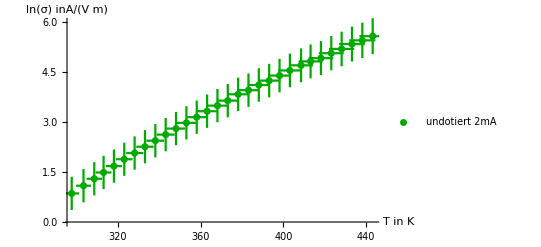

```mathematica
errPlotM2i1=ErrorListPlot[plotValuesM2i1,AxesLabel->{"T in  K","ln(σ) inA/(V m)"},PlotRange->{0,6},PlotStyle-> {Darker[Green]},PlotLegends->Placed[{"undotiert 2mA"},{.75,.25}]]
```

## M2 undotiert I=3mA

### Plotten (Vorbereitung) Leitfähigkeit gegen T

```mathematica
pointsM2i2=Partition[Flatten[Riffle[T2K,leitf2ln]],2];
```

```mathematica
Length[T2K]
```

20

```mathematica
errorsM2i2=Table[ErrorBar[T2GradErr[[i ]],leitf2lnErr[[i]]],{i,1,20}]
```

{ErrorBar[3.528,0.333393],ErrorBar[3.776,0.33341],ErrorBar[4.112,0.33346],ErrorBar[4.332,0.333525],ErrorBar[4.384,0.333547],ErrorBar[4.536,0.333628],ErrorBar[4.53,0.333623],ErrorBar[4.766,0.33385],ErrorBar[4.87,0.334002],ErrorBar[4.988,0.334231],ErrorBar[5.1,0.334514],ErrorBar[5.158,0.3347],ErrorBar[5.184,0.334845],ErrorBar[5.38,0.33576],ErrorBar[5.59,0.337346],ErrorBar[5.778,0.339848],ErrorBar[5.896,0.341983],ErrorBar[6.034,0.345456],ErrorBar[6.252,0.352977],ErrorBar[6.42,0.36207]}

```mathematica
plotValuesM2i2=Partition[Riffle[pointsM2i2,errorsM2i2],2]
```

{{{299.55,0.945462},ErrorBar[3.528,0.333393]},{{311.95,1.45529},ErrorBar[3.776,0.33341]},{{328.75,2.12444},ErrorBar[4.112,0.33346]},{{339.75,2.5341},ErrorBar[4.332,0.333525]},{{342.35,2.63109},ErrorBar[4.384,0.333547]},{{349.95,2.89137},ErrorBar[4.536,0.333628]},{{349.65,2.87943},ErrorBar[4.53,0.333623]},{{361.45,3.30135},ErrorBar[4.766,0.33385]},{{366.65,3.47377},ErrorBar[4.87,0.334002]},{{372.55,3.66256},ErrorBar[4.988,0.334231]},{{378.15,3.83198},ErrorBar[5.1,0.334514]},{{381.05,3.92039},ErrorBar[5.158,0.3347]},{{382.35,3.98102},ErrorBar[5.184,0.334845]},{{392.15,4.25686},ErrorBar[5.38,0.33576]},{{402.65,4.54063},ErrorBar[5.59,0.337346]},{{412.05,4.80769},ErrorBar[5.778,0.339848]},{{417.95,4.96185},ErrorBar[5.896,0.341983]},{{424.85,5.14417},ErrorBar[6.034,0.345456]},{{435.75,5.40368},ErrorBar[6.252,0.352977]},{{444.15,5.60847},ErrorBar[6.42,0.36207]}}

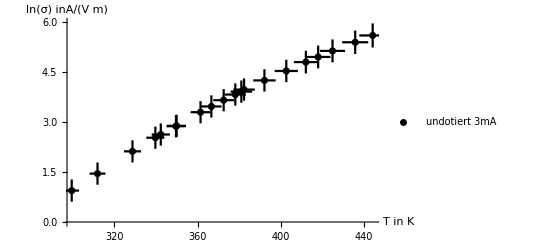

```mathematica
errPlotM2i2=ErrorListPlot[plotValuesM2i2,AxesLabel->{"T in  K","ln(σ) inA/(V m)"},PlotRange->{0,6},PlotStyle-> {Black},PlotLegends->Placed[{"undotiert 3mA"},{.75,.35}]]
```

## M2 Ergebnis

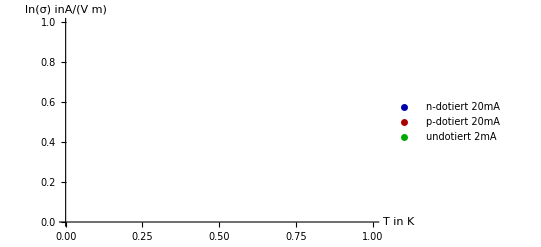

```mathematica
Show[errPlotM2n1,errPlotM2p1,errPlotM2i1]
```

```mathematica
Show[errPlotM2n1Range35,errPlotM2p1Range35]
```

-Graphics-

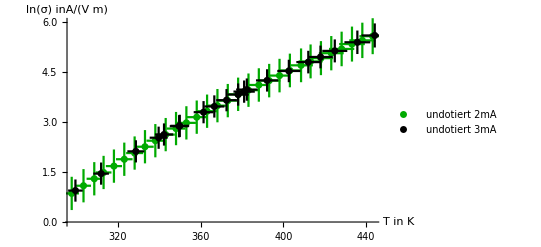

```mathematica
Show[errPlotM2i1,errPlotM2i2]
```

M3

## M3.1

### Messwerte

```mathematica
messwerteM31n=({{0.0, 3.0, 5.4, 10.0, 15.1, 20.0, 25.2, 29.8}, {0.0, 2.0, 3.6, 6.6, 10.0, 13.2, 16.6, 19.7}})
```

{{0.,3.,5.4,10.,15.1,20.,25.2,29.8},{0.,2.,3.6,6.6,10.,13.2,16.6,19.7}}

```mathematica
messwerteM31p=({{0.0, 3.0, 5.1, 9.9, 15.0, 20.3, 25.2, 29.7}, {0.0, 2.1, 3.6, 7.0, 10.6, 14.4, 17.9, 21.1}})
```

{{0.,3.,5.1,9.9,15.,20.3,25.2,29.7},{0.,2.1,3.6,7.,10.6,14.4,17.9,21.1}}

```mathematica
M31ni=messwerteM31n[[1]]*10^-3
```

{0.,0.003,0.0054,0.01,0.0151,0.02,0.0252,0.0298}

```mathematica
M31nu=messwerteM31n[[2]]*10^-3
```

{0.,0.002,0.0036,0.0066,0.01,0.0132,0.0166,0.0197}

```mathematica
M31pi=messwerteM31p[[1]]*10^-3
```

{0.,0.003,0.0051,0.0099,0.015,0.0203,0.0252,0.0297}

```mathematica
M31pu=messwerteM31p[[2]]*10^-3
```

{0.,0.0021,0.0036,0.007,0.0106,0.0144,0.0179,0.0211}

### Fehler

```mathematica
messfehlerM31u[x_]:=0.1*10^-3*3+x*0.005; (*0.1mV Auflösung 3dgts + 0.5%*)
```

```mathematica
fehlerM31nu=messfehlerM31u[#] & /@ M31nu
```

{0.0003,0.00031,0.000318,0.000333,0.00035,0.000366,0.000383,0.0003985}

```mathematica
messfehlerM31i[x_]:=1*10^-3;
```

```mathematica
fehlerM31ni=messfehlerM31i[#] & /@ M31ni
```

{1/1000,1/1000,1/1000,1/1000,1/1000,1/1000,1/1000,1/1000}

```mathematica
fehlerM31pu=messfehlerM31u[#] & /@ M31pu
```

{0.0003,0.0003105,0.000318,0.000335,0.000353,0.000372,0.0003895,0.0004055}

```mathematica
fehlerM31pi=messfehlerM31i[#] & /@ M31pi
```

{1/1000,1/1000,1/1000,1/1000,1/1000,1/1000,1/1000,1/1000}

### Plot

```mathematica
pointsM31n=Partition[Flatten[Riffle[M31ni,M31nu]],2];
```

```mathematica
Length[M31ni]
```

8

```mathematica
errorsM31n=Table[ErrorBar[fehlerM31ni[[i ]],fehlerM31nu[[i]]],{i,1,8}]
```

{ErrorBar[1/1000,0.0003],ErrorBar[1/1000,0.00031],ErrorBar[1/1000,0.000318],ErrorBar[1/1000,0.000333],ErrorBar[1/1000,0.00035],ErrorBar[1/1000,0.000366],ErrorBar[1/1000,0.000383],ErrorBar[1/1000,0.0003985]}

```mathematica
plotValuesM31n=Partition[Riffle[pointsM31n,errorsM31n],2]
```

{{{0.,0.},ErrorBar[1/1000,0.0003]},{{0.003,0.002},ErrorBar[1/1000,0.00031]},{{0.0054,0.0036},ErrorBar[1/1000,0.000318]},{{0.01,0.0066},ErrorBar[1/1000,0.000333]},{{0.0151,0.01},ErrorBar[1/1000,0.00035]},{{0.02,0.0132},ErrorBar[1/1000,0.000366]},{{0.0252,0.0166},ErrorBar[1/1000,0.000383]},{{0.0298,0.0197},ErrorBar[1/1000,0.0003985]}}

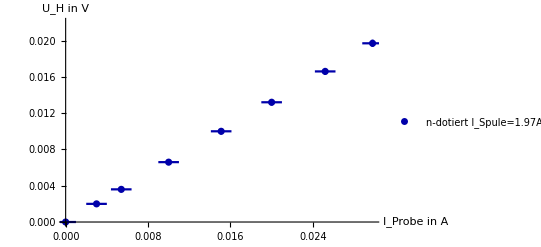

```mathematica
errPlotM31n=ErrorListPlot[plotValuesM31n,AxesLabel->{"I_Probe in A","U_H in  V"},PlotRange->{0,0.022},PlotStyle-> {Darker[Blue]},PlotLegends->Placed[{"n-dotiert I_Spule=1.97A"},{.75,.25}]]
```

```mathematica
pointsM31p=Partition[Flatten[Riffle[M31pi,M31pu]],2];
```

```mathematica
Length[M31pi]
```

8

```mathematica
errorsM31p=Table[ErrorBar[fehlerM31pi[[i ]],fehlerM31pu[[i]]],{i,1,8}]
```

{ErrorBar[1/1000,0.0003],ErrorBar[1/1000,0.0003105],ErrorBar[1/1000,0.000318],ErrorBar[1/1000,0.000335],ErrorBar[1/1000,0.000353],ErrorBar[1/1000,0.000372],ErrorBar[1/1000,0.0003895],ErrorBar[1/1000,0.0004055]}

```mathematica
plotValuesM31p=Partition[Riffle[pointsM31p,errorsM31p],2]
```

{{{0.,0.},ErrorBar[1/1000,0.0003]},{{0.003,0.0021},ErrorBar[1/1000,0.0003105]},{{0.0051,0.0036},ErrorBar[1/1000,0.000318]},{{0.0099,0.007},ErrorBar[1/1000,0.000335]},{{0.015,0.0106},ErrorBar[1/1000,0.000353]},{{0.0203,0.0144},ErrorBar[1/1000,0.000372]},{{0.0252,0.0179},ErrorBar[1/1000,0.0003895]},{{0.0297,0.0211},ErrorBar[1/1000,0.0004055]}}

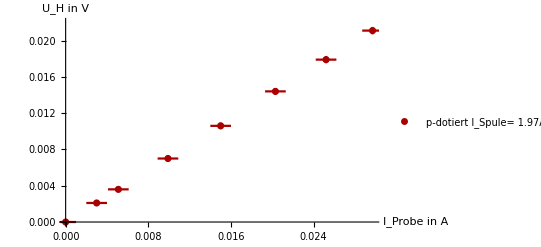

```mathematica
errPlotM31p=ErrorListPlot[plotValuesM31p,AxesLabel->{"I_Probe in A","U_H in  V"},PlotRange->{0,0.022},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert I_Spule= 1.97A"},{.75,.35}]]
```

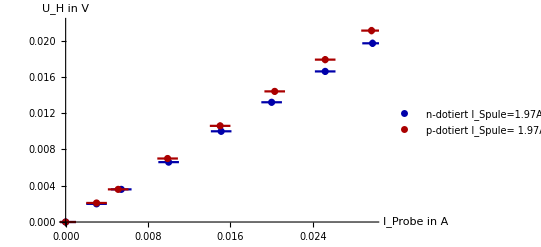

```mathematica
Show[errPlotM31n,errPlotM31p]
```

### Fit (Berechnung) n-dotiert

```mathematica
lmM31nXYErr=LinearModelFit[pointsM31n,x,x,Weights->1/(fehlerM31nu^2+(0.6596418722584753)^2*fehlerM31ni^2),IncludeConstantBasis->True]
```

FittedModel[0.0000163425+0.659624 x]

```mathematica
lmM31nYErr=LinearModelFit[pointsM31n,x,x,Weights->1/fehlerM31nu^2,IncludeConstantBasis->True]
```

FittedModel[0.0000161056+0.659642 x]

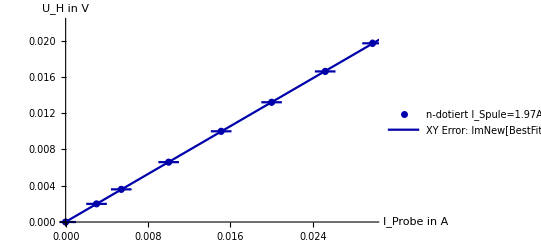

```mathematica
M31nFit=Show[errPlotM31n, Plot[{Normal[lmM31nXYErr]},{x,0,0.05}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Darker[Blue]}]]
```

```mathematica
lmM31nXYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{0.0000163425+0.659624 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0000163425 | 0.0000144155 | 1.13367 | 0.300188
x | 0.659624 | 0.000871151 | 757.187 | 3.58157×10^-16, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 634.819 | 634.819 | 573332. | 3.58157×10^-16
Error | 6 | 0.00664347 | 0.00110725 |  | 
Total | 7 | 634.826 |  |  | ,0.99999,0.999988}

Steigung= (0.65962+-0.00087) X und Y Gewicht und y-Achsenabschnitt= (0.000016 +- 0.000014) n-dotiert

### Fit (Berechnung) p-dotiert

```mathematica
lmM31pXYErr=LinearModelFit[pointsM31p,x,x,Weights->1/(fehlerM31pu^2+(+0.7106564746450205 )^2*fehlerM31pi^2),IncludeConstantBasis->True]
```

FittedModel[-0.0000267981+0.710852 x]

```mathematica
lmM31pYErr=LinearModelFit[pointsM31p,x,x,Weights->1/fehlerM31pu^2,IncludeConstantBasis->True]
```

FittedModel[-0.0000242648+0.710656 x]

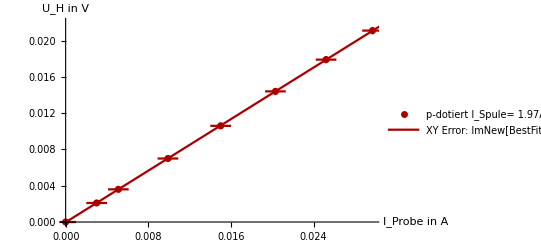

```mathematica
M31pFit=Show[errPlotM31p, Plot[{Normal[lmM31pXYErr]},{x,0,0.05}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Darker[Red]}]]
```

```mathematica
lmM31pXYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{-0.0000267981+0.710852 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0000267981 | 0.0000120077 | -2.23175 | 0.0671045
x | 0.710852 | 0.000725456 | 979.869 | 7.62587×10^-17, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 657.425 | 657.425 | 960143. | 7.62587×10^-17
Error | 6 | 0.0041083 | 0.000684716 |  | 
Total | 7 | 657.429 |  |  | ,0.999994,0.999993}

Steigung= (.71085+-0.00073) X und Y Gewicht und y-Achsenabschnitt= (-0.000027 +- 0.000012) p-dotiert

## Ergebnis M3.1 Fit

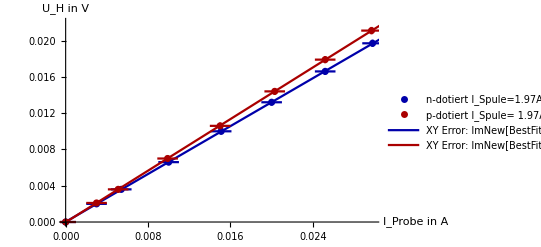

```mathematica
Show[M31nFit,M31pFit]
```

Steigung= (0.71085+-0.00073) X und Y Gewicht und y-Achsenabschnitt= (-0.000027 +- 0.000012) p-dotiert

Steigung= (0.65962+-0.00087) X und Y Gewicht und y-Achsenabschnitt= (0.000016 +- 0.000014) n-dotiert

```mathematica
0.00073/0.71085
```

0.00102694

```mathematica
1/(-0.000027/0.000012)
```

-0.444444

```mathematica
1/(0.65962/ 0.00087)
```

0.00131894

```mathematica
1/(-0.000016/0.000014)
```

-0.875

## M3.2

### Messwerte

```mathematica
messwerteM32n=({{.11, .20, .33, .41, .59, .89, 1.15, 1.33, 1.53, 1.74, 1.92}, {0.9, 1.9, 2.3, 2.9, 3.8, 6.2, 7.9, 9.2, 10.5, 12.0, 13.1}})
```

{{0.11,0.2,0.33,0.41,0.59,0.89,1.15,1.33,1.53,1.74,1.92},{0.9,1.9,2.3,2.9,3.8,6.2,7.9,9.2,10.5,12.,13.1}}

```mathematica
messwerteM32p=({{0.00, .23, .45, .61, .80, 1.01, 1.20, 1.40, 1.62, 1.82, 1.97}, {.2, 1.8, 3.3, 4.4, 5.8, 7.3, 8.7, 10.2, 11.7, 13.1, 14.2}})
```

{{0.,0.23,0.45,0.61,0.8,1.01,1.2,1.4,1.62,1.82,1.97},{0.2,1.8,3.3,4.4,5.8,7.3,8.7,10.2,11.7,13.1,14.2}}

```mathematica
M32ni=messwerteM32n[[1]]
```

{0.11,0.2,0.33,0.41,0.59,0.89,1.15,1.33,1.53,1.74,1.92}

```mathematica
M32nu=messwerteM32n[[2]]*10^-3
```

{0.0009,0.0019,0.0023,0.0029,0.0038,0.0062,0.0079,0.0092,0.0105,0.012,0.0131}

```mathematica
M32pi=messwerteM32p[[1]]
```

{0.,0.23,0.45,0.61,0.8,1.01,1.2,1.4,1.62,1.82,1.97}

```mathematica
M32pu=messwerteM32p[[2]]*10^-3
```

{0.0002,0.0018,0.0033,0.0044,0.0058,0.0073,0.0087,0.0102,0.0117,0.0131,0.0142}

### Fehler

```mathematica
messfehlerM32u[x_]:=0.1*10^-3*3+x*0.005;
```

```mathematica
fehlerM32nu=messfehlerM32u[#] & /@ M32nu
```

{0.0003045,0.0003095,0.0003115,0.0003145,0.000319,0.000331,0.0003395,0.000346,0.0003525,0.00036,0.0003655}

```mathematica
messfehlerM32i[x_]:=0.01*3+x*0.015; (*Auflösung 0.01 A*)
```

```mathematica
fehlerM32ni=messfehlerM32i[#] & /@ M32ni
```

{0.03165,0.033,0.03495,0.03615,0.03885,0.04335,0.04725,0.04995,0.05295,0.0561,0.0588}

```mathematica
fehlerM32pu=messfehlerM32u[#] & /@ M32pu
```

{0.000301,0.000309,0.0003165,0.000322,0.000329,0.0003365,0.0003435,0.000351,0.0003585,0.0003655,0.000371}

```mathematica
fehlerM32pi=messfehlerM32i[#] & /@ M32pi
```

{0.03,0.03345,0.03675,0.03915,0.042,0.04515,0.048,0.051,0.0543,0.0573,0.05955}

### Plot

```mathematica
pointsM32n=Partition[Flatten[Riffle[M32ni,M32nu]],2];
```

```mathematica
Length[M32ni]
```

11

```mathematica
errorsM32n=Table[ErrorBar[fehlerM32ni[[i ]],fehlerM32nu[[i]]],{i,1,11}]
```

{ErrorBar[0.03165,0.0003045],ErrorBar[0.033,0.0003095],ErrorBar[0.03495,0.0003115],ErrorBar[0.03615,0.0003145],ErrorBar[0.03885,0.000319],ErrorBar[0.04335,0.000331],ErrorBar[0.04725,0.0003395],ErrorBar[0.04995,0.000346],ErrorBar[0.05295,0.0003525],ErrorBar[0.0561,0.00036],ErrorBar[0.0588,0.0003655]}

```mathematica
plotValuesM32n=Partition[Riffle[pointsM32n,errorsM32n],2]
```

{{{0.11,0.0009},ErrorBar[0.03165,0.0003045]},{{0.2,0.0019},ErrorBar[0.033,0.0003095]},{{0.33,0.0023},ErrorBar[0.03495,0.0003115]},{{0.41,0.0029},ErrorBar[0.03615,0.0003145]},{{0.59,0.0038},ErrorBar[0.03885,0.000319]},{{0.89,0.0062},ErrorBar[0.04335,0.000331]},{{1.15,0.0079},ErrorBar[0.04725,0.0003395]},{{1.33,0.0092},ErrorBar[0.04995,0.000346]},{{1.53,0.0105},ErrorBar[0.05295,0.0003525]},{{1.74,0.012},ErrorBar[0.0561,0.00036]},{{1.92,0.0131},ErrorBar[0.0588,0.0003655]}}

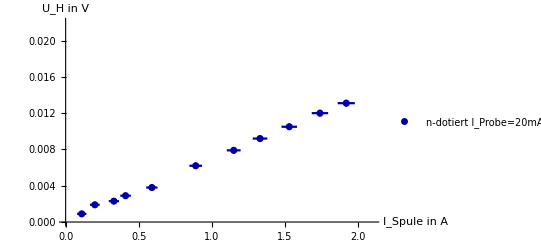

```mathematica
errPlotM32n=ErrorListPlot[plotValuesM32n,AxesLabel->{"I_Spule in A","U_H in  V"},PlotRange->{{0,2.1},{0,0.022}},PlotStyle-> {Darker[Blue]},PlotLegends->Placed[{"n-dotiert I_Probe=20mA"},{.35,.65}]]
```

```mathematica
pointsM32p=Partition[Flatten[Riffle[M32pi,M32pu]],2];
```

```mathematica
Length[M32pi]
```

11

```mathematica
errorsM32p=Table[ErrorBar[fehlerM32pi[[i ]],fehlerM32pu[[i]]],{i,1,11}]
```

{ErrorBar[0.03,0.000301],ErrorBar[0.03345,0.000309],ErrorBar[0.03675,0.0003165],ErrorBar[0.03915,0.000322],ErrorBar[0.042,0.000329],ErrorBar[0.04515,0.0003365],ErrorBar[0.048,0.0003435],ErrorBar[0.051,0.000351],ErrorBar[0.0543,0.0003585],ErrorBar[0.0573,0.0003655],ErrorBar[0.05955,0.000371]}

```mathematica
plotValuesM32p=Partition[Riffle[pointsM32p,errorsM32p],2]
```

{{{0.,0.0002},ErrorBar[0.03,0.000301]},{{0.23,0.0018},ErrorBar[0.03345,0.000309]},{{0.45,0.0033},ErrorBar[0.03675,0.0003165]},{{0.61,0.0044},ErrorBar[0.03915,0.000322]},{{0.8,0.0058},ErrorBar[0.042,0.000329]},{{1.01,0.0073},ErrorBar[0.04515,0.0003365]},{{1.2,0.0087},ErrorBar[0.048,0.0003435]},{{1.4,0.0102},ErrorBar[0.051,0.000351]},{{1.62,0.0117},ErrorBar[0.0543,0.0003585]},{{1.82,0.0131},ErrorBar[0.0573,0.0003655]},{{1.97,0.0142},ErrorBar[0.05955,0.000371]}}

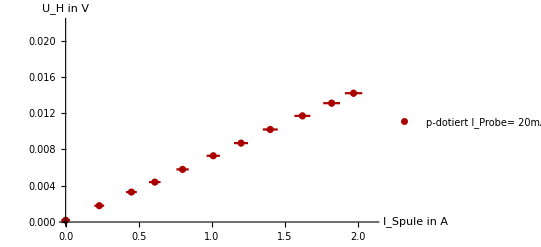

```mathematica
errPlotM32p=ErrorListPlot[plotValuesM32p,AxesLabel->{"I_Spule in A","U_H in  V"},PlotRange->{{0,2.1},{0,0.022}},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert I_Probe= 20mA"},{.35,.75}]]
```

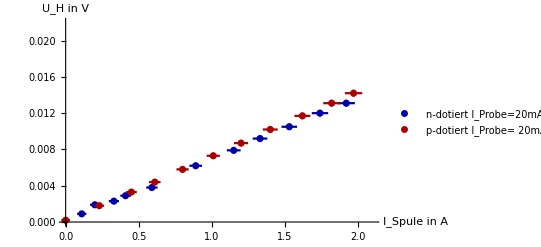

```mathematica
Show[errPlotM32n,errPlotM32p]
```

### Fit (Berechnung) n-dotiert

```mathematica
lmM32nXYErr=LinearModelFit[pointsM32n,x,x,Weights->1/(fehlerM32nu^2+(0.006739220804468463)^2*fehlerM32ni^2),IncludeConstantBasis->True]
```

FittedModel[0.000186004+0.00672915 x]

```mathematica
lmM32nYErr=LinearModelFit[pointsM32n,x,x,Weights->1/fehlerM32nu^2,IncludeConstantBasis->True]
```

FittedModel[0.000177177+0.00673922 x]

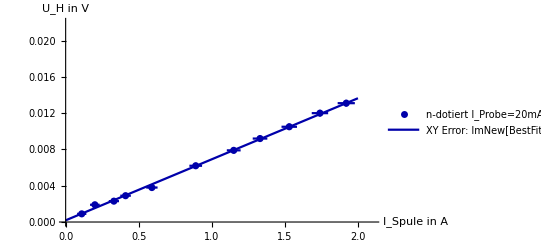

```mathematica
M32nFit=Show[errPlotM32n, Plot[{Normal[lmM32nXYErr]},{x,0,2.0}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Darker[Blue]}]]
```

```mathematica
lmM32nXYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{0.000186004+0.00672915 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.000186004 | 0.0000982805 | 1.89258 | 0.0909605
x | 0.00672915 | 0.000100879 | 66.705 | 1.93133×10^-13, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 907.861 | 907.861 | 4449.56 | 1.93133×10^-13
Error | 9 | 1.83631 | 0.204034 |  | 
Total | 10 | 909.697 |  |  | ,0.997981,0.997757}

Steigung= (0.00673+-0.00010) X und Y Gewicht und y-Achsenabschnitt= (0.000186 +- 0.000098) n-dotiert

### Fit (Berechnung) p-dotiert

```mathematica
lmM32pXYErr=LinearModelFit[pointsM32p,x,x,Weights->1/(fehlerM32pu^2+(0.007133113121769784 )^2*fehlerM32pi^2),IncludeConstantBasis->True]
```

FittedModel[0.000136876+0.00712757 x]

```mathematica
lmM32pYErr=LinearModelFit[pointsM32p,x,x,Weights->1/fehlerM32pu^2,IncludeConstantBasis->True]
```

FittedModel[0.000131754+0.00713311 x]

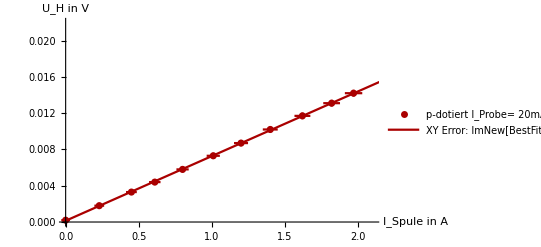

```mathematica
M32pFit=Show[errPlotM32p, Plot[{Normal[lmM32pXYErr]},{x,0,2.5}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Darker[Red]}]]
```

```mathematica
lmM32pXYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{0.000136876+0.00712757 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.000136876 | 0.0000278257 | 4.91906 | 0.00082568
x | 0.00712757 | 0.0000266591 | 267.36 | 7.29098×10^-19, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 1022.06 | 1022.06 | 71481.1 | 7.29098×10^-19
Error | 9 | 0.128685 | 0.0142983 |  | 
Total | 10 | 1022.19 |  |  | ,0.999874,0.99986}

Steigung= (0.00712757+-0.000027) X und Y Gewicht und y-Achsenabschnitt= (0.000137+- 0.000028) p-dotiert

## Ergebnis M3.2 Fit

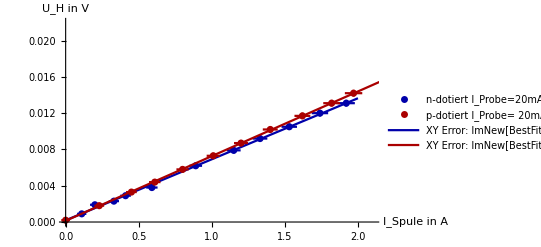

```mathematica
Show[M32nFit,M32pFit]
```

Steigung= (0.00712757+-0.000027) X und Y Gewicht und y-Achsenabschnitt= (0.000137+- 0.000028) p-dotiert  T=300.9K

Steigung= (0.00673+-0.00010) X und Y Gewicht und y-Achsenabschnitt= (0.000186 +- 0.000098) n-dotiert T=299.9K

```mathematica
27.7+273.15
```

300.85

```mathematica
1/(0.000137/0.000028)
```

0.20438

```mathematica
1/(0.00673/0.00010)
```

0.0148588

```mathematica
1/(0.000186/0.000098)
```

0.526882

## M3.3

### Messwerte

```mathematica
messwerteM33pGleichgewicht=({{28.4, 61.2, 71.6, 92.0, 100.4, 116.4, 125.8, 132.1, 137.1, 145.7, 160.5, 171.4}, {14.2, 13.2, 12.0, 6.7, 4.2, 1.0, .3, .1, 0.0, .1, .3, .4}})
```

{{28.4,61.2,71.6,92.,100.4,116.4,125.8,132.1,137.1,145.7,160.5,171.4},{14.2,13.2,12.,6.7,4.2,1.,0.3,0.1,0.,0.1,0.3,0.4}}

```mathematica
messwerteM33pAbkuehlen=({{37.3, 40.7, 50.0, 53.0, 60.0, 65.0, 68.3, 75.0, 79.0, 87.0, 97.0, 110.0, 115.0, 128.0, 133.0, 137.0, 145.0, 153.0}, {14.2, 14.1, 13.8, 13.7, 13.2, 12.6, 12.2, 11.2, 10.2, 8.0, 5.2, 1.8, 1.1, .3, .1, .1, .1, .2}})
```

{{37.3,40.7,50.,53.,60.,65.,68.3,75.,79.,87.,97.,110.,115.,128.,133.,137.,145.,153.},{14.2,14.1,13.8,13.7,13.2,12.6,12.2,11.2,10.2,8.,5.2,1.8,1.1,0.3,0.1,0.1,0.1,0.2}}

```mathematica
messwerteM33nGleichgewicht=({{27.2, 49.2, 62.6, 84, 96.6, 120.4, 144.0, 153.0, 164.6, 170.0}, {10.1, 10.2, 9.8, 8.0, 6.2, 2.9, 1.1, .7, .3, .1}})
```

{{27.2,49.2,62.6,84,96.6,120.4,144.,153.,164.6,170.},{10.1,10.2,9.8,8.,6.2,2.9,1.1,0.7,0.3,0.1}}

```mathematica
messwerteM33nAbkuehlen=({{45, 50, 60, 70, 80, 90, 100, 110, 120, 130, 145}, {10.0, 10.0, 9.8, 9.3, 8.3, 6.8, 5.2, 3.8, 2.6, 1.8, .9}})
```

{{45,50,60,70,80,90,100,110,120,130,145},{10.,10.,9.8,9.3,8.3,6.8,5.2,3.8,2.6,1.8,0.9}}

```mathematica
M33pGT=messwerteM33pGleichgewicht[[1]]
```

{28.4,61.2,71.6,92.,100.4,116.4,125.8,132.1,137.1,145.7,160.5,171.4}

```mathematica
M33pGU=messwerteM33pGleichgewicht[[2]]*10^-3
```

{0.0142,0.0132,0.012,0.0067,0.0042,0.001,0.0003,0.0001,0.,0.0001,0.0003,0.0004}

```mathematica
M33nGT=messwerteM33nGleichgewicht[[1]]
```

{27.2,49.2,62.6,84,96.6,120.4,144.,153.,164.6,170.}

```mathematica
M33nGU=messwerteM33nGleichgewicht[[2]]*10^-3
```

{0.0101,0.0102,0.0098,0.008,0.0062,0.0029,0.0011,0.0007,0.0003,0.0001}

```mathematica
M33pAT=messwerteM33pAbkuehlen[[1]]
```

{37.3,40.7,50.,53.,60.,65.,68.3,75.,79.,87.,97.,110.,115.,128.,133.,137.,145.,153.}

```mathematica
M33pAU=messwerteM33pAbkuehlen[[2]]*10^-3
```

{0.0142,0.0141,0.0138,0.0137,0.0132,0.0126,0.0122,0.0112,0.0102,0.008,0.0052,0.0018,0.0011,0.0003,0.0001,0.0001,0.0001,0.0002}

```mathematica
M33nAT=messwerteM33nAbkuehlen[[1]]
```

{45,50,60,70,80,90,100,110,120,130,145}

```mathematica
M33nAU=messwerteM33nAbkuehlen[[2]]*10^-3
```

{0.01,0.01,0.0098,0.0093,0.0083,0.0068,0.0052,0.0038,0.0026,0.0018,0.0009}

```mathematica
inK[x_]:=x+273.15;
```

```mathematica
M33nGTK=inK[#]&/@M33nGT
```

{300.35,322.35,335.75,357.15,369.75,393.55,417.15,426.15,437.75,443.15}

```mathematica
M33nATK=inK[#]&/@M33nAT
```

{318.15,323.15,333.15,343.15,353.15,363.15,373.15,383.15,393.15,403.15,418.15}

```mathematica
M33pGTK=inK[#]&/@M33pGT
```

{301.55,334.35,344.75,365.15,373.55,389.55,398.95,405.25,410.25,418.85,433.65,444.55}

```mathematica
M33pATK=inK[#]&/@M33pAT
```

{310.45,313.85,323.15,326.15,333.15,338.15,341.45,348.15,352.15,360.15,370.15,383.15,388.15,401.15,406.15,410.15,418.15,426.15}

### Fehler

```mathematica
messfehlerM33u[x_]:=0.1*10^-3*3+x*0.005;
```

```mathematica
fehlerM33nGU=messfehlerM33u[#] & /@ M33nGU
```

{0.0003505,0.000351,0.000349,0.00034,0.000331,0.0003145,0.0003055,0.0003035,0.0003015,0.0003005}

```mathematica
fehlerM33pGU=messfehlerM33u[#] & /@ M33pGU
```

{0.000371,0.000366,0.00036,0.0003335,0.000321,0.000305,0.0003015,0.0003005,0.0003,0.0003005,0.0003015,0.000302}

```mathematica
fehlerM33pAU=messfehlerM33u[#] & /@ M33pAU
```

{0.000371,0.0003705,0.000369,0.0003685,0.000366,0.000363,0.000361,0.000356,0.000351,0.00034,0.000326,0.000309,0.0003055,0.0003015,0.0003005,0.0003005,0.0003005,0.000301}

```mathematica
fehlerM33nAU=messfehlerM33u[#] & /@ M33nAU
```

{0.00035,0.00035,0.000349,0.0003465,0.0003415,0.000334,0.000326,0.000319,0.000313,0.000309,0.0003045}

```mathematica
messfehlerM33T[x_]:=3+x*0.02; (*3Grad + 2%*)
```

```mathematica
fehlerM33nGT=messfehlerM33T[#] & /@ M33nGT
```

{3.544,3.984,4.252,4.68,4.932,5.408,5.88,6.06,6.292,6.4}

```mathematica
fehlerM33pGT=messfehlerM33T[#] & /@ M33pGT
```

{3.568,4.224,4.432,4.84,5.008,5.328,5.516,5.642,5.742,5.914,6.21,6.428}

```mathematica
fehlerM33pAT=messfehlerM33T[#] & /@ M33pAT
```

{3.746,3.814,4.,4.06,4.2,4.3,4.366,4.5,4.58,4.74,4.94,5.2,5.3,5.56,5.66,5.74,5.9,6.06}

```mathematica
fehlerM33nAT=messfehlerM33T[#] & /@ M33nAT
```

{3.9,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.9}

### Plot

```mathematica
pointsM33nG=Partition[Flatten[Riffle[M33nGTK,M33nGU]],2];
```

```mathematica
Length[M33nGU]
```

10

```mathematica
errorsM33nG=Table[ErrorBar[fehlerM33nGT[[i ]],fehlerM33nGU[[i]]],{i,1,10}]
```

{ErrorBar[3.544,0.0003505],ErrorBar[3.984,0.000351],ErrorBar[4.252,0.000349],ErrorBar[4.68,0.00034],ErrorBar[4.932,0.000331],ErrorBar[5.408,0.0003145],ErrorBar[5.88,0.0003055],ErrorBar[6.06,0.0003035],ErrorBar[6.292,0.0003015],ErrorBar[6.4,0.0003005]}

```mathematica
plotValuesM33nG=Partition[Riffle[pointsM33nG,errorsM33nG],2]
```

{{{300.35,0.0101},ErrorBar[3.544,0.0003505]},{{322.35,0.0102},ErrorBar[3.984,0.000351]},{{335.75,0.0098},ErrorBar[4.252,0.000349]},{{357.15,0.008},ErrorBar[4.68,0.00034]},{{369.75,0.0062},ErrorBar[4.932,0.000331]},{{393.55,0.0029},ErrorBar[5.408,0.0003145]},{{417.15,0.0011},ErrorBar[5.88,0.0003055]},{{426.15,0.0007},ErrorBar[6.06,0.0003035]},{{437.75,0.0003},ErrorBar[6.292,0.0003015]},{{443.15,0.0001},ErrorBar[6.4,0.0003005]}}

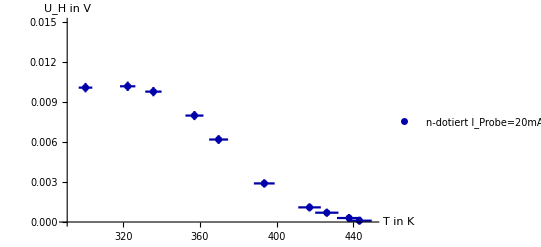

```mathematica
errPlotM33nG=ErrorListPlot[plotValuesM33nG,AxesLabel->{"T in K","U_H in  V"},PlotRange->{{290,450},{0,.015}},PlotStyle-> {Darker[Blue]},PlotLegends->Placed[{"n-dotiert I_Probe=20mA"},{.75,.65}]]
```

```mathematica
pointsM33pG=Partition[Flatten[Riffle[M33pGTK,M33pGU]],2];
```

```mathematica
Length[M33pGU]
```

12

```mathematica
errorsM33pG=Table[ErrorBar[fehlerM33pGT[[i ]],fehlerM33pGU[[i]]],{i,1,12}]
```

{ErrorBar[3.568,0.000371],ErrorBar[4.224,0.000366],ErrorBar[4.432,0.00036],ErrorBar[4.84,0.0003335],ErrorBar[5.008,0.000321],ErrorBar[5.328,0.000305],ErrorBar[5.516,0.0003015],ErrorBar[5.642,0.0003005],ErrorBar[5.742,0.0003],ErrorBar[5.914,0.0003005],ErrorBar[6.21,0.0003015],ErrorBar[6.428,0.000302]}

```mathematica
plotValuesM33pG=Partition[Riffle[pointsM33pG,errorsM33pG],2]
```

{{{301.55,0.0142},ErrorBar[3.568,0.000371]},{{334.35,0.0132},ErrorBar[4.224,0.000366]},{{344.75,0.012},ErrorBar[4.432,0.00036]},{{365.15,0.0067},ErrorBar[4.84,0.0003335]},{{373.55,0.0042},ErrorBar[5.008,0.000321]},{{389.55,0.001},ErrorBar[5.328,0.000305]},{{398.95,0.0003},ErrorBar[5.516,0.0003015]},{{405.25,0.0001},ErrorBar[5.642,0.0003005]},{{410.25,0.},ErrorBar[5.742,0.0003]},{{418.85,0.0001},ErrorBar[5.914,0.0003005]},{{433.65,0.0003},ErrorBar[6.21,0.0003015]},{{444.55,0.0004},ErrorBar[6.428,0.000302]}}

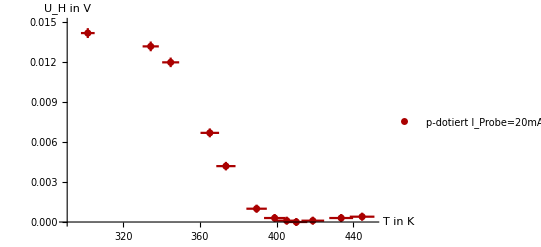

```mathematica
errPlotM33pG=ErrorListPlot[plotValuesM33pG,AxesLabel->{"T in K","U_H in  V"},PlotRange->{{290,450},{0,.015}},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert I_Probe=20mA"},{.75,.75}]]
```

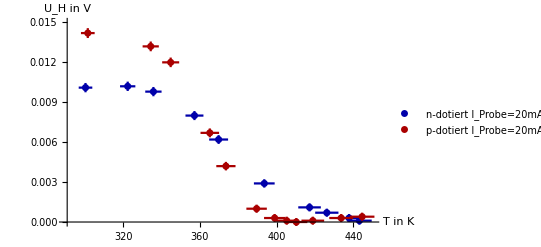

```mathematica
Show[errPlotM33nG,errPlotM33pG]
```

### Plot Abkühlen

```mathematica
pointsM33nA=Partition[Flatten[Riffle[M33nATK,M33nAU]],2];
```

```mathematica
Length[M33nAU]
```

11

```mathematica
errorsM33nA=Table[ErrorBar[fehlerM33nAT[[i ]],fehlerM33nAU[[i]]],{i,1,11}]
```

{ErrorBar[3.9,0.00035],ErrorBar[4.,0.00035],ErrorBar[4.2,0.000349],ErrorBar[4.4,0.0003465],ErrorBar[4.6,0.0003415],ErrorBar[4.8,0.000334],ErrorBar[5.,0.000326],ErrorBar[5.2,0.000319],ErrorBar[5.4,0.000313],ErrorBar[5.6,0.000309],ErrorBar[5.9,0.0003045]}

```mathematica
plotValuesM33nA=Partition[Riffle[pointsM33nA,errorsM33nA],2]
```

{{{318.15,0.01},ErrorBar[3.9,0.00035]},{{323.15,0.01},ErrorBar[4.,0.00035]},{{333.15,0.0098},ErrorBar[4.2,0.000349]},{{343.15,0.0093},ErrorBar[4.4,0.0003465]},{{353.15,0.0083},ErrorBar[4.6,0.0003415]},{{363.15,0.0068},ErrorBar[4.8,0.000334]},{{373.15,0.0052},ErrorBar[5.,0.000326]},{{383.15,0.0038},ErrorBar[5.2,0.000319]},{{393.15,0.0026},ErrorBar[5.4,0.000313]},{{403.15,0.0018},ErrorBar[5.6,0.000309]},{{418.15,0.0009},ErrorBar[5.9,0.0003045]}}

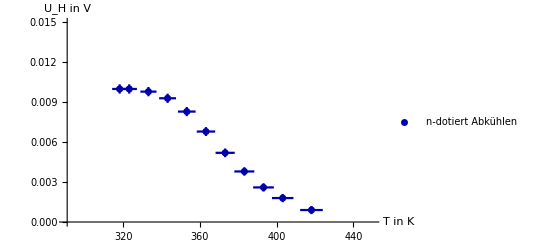

```mathematica
errPlotM33nA=ErrorListPlot[plotValuesM33nA,AxesLabel->{"T in K","U_H in  V"},PlotRange->{{290,450},{0,.015}},PlotStyle-> {Darker[Blue]},PlotLegends->Placed[{"n-dotiert Abkühlen"},{.75,.65}]]
```

```mathematica
pointsM33pA=Partition[Flatten[Riffle[M33pATK,M33pAU]],2];
```

```mathematica
Length[M33pAU]
```

18

```mathematica
errorsM33pA=Table[ErrorBar[fehlerM33pAT[[i ]],fehlerM33pAU[[i]]],{i,1,18}]
```

{ErrorBar[3.746,0.000371],ErrorBar[3.814,0.0003705],ErrorBar[4.,0.000369],ErrorBar[4.06,0.0003685],ErrorBar[4.2,0.000366],ErrorBar[4.3,0.000363],ErrorBar[4.366,0.000361],ErrorBar[4.5,0.000356],ErrorBar[4.58,0.000351],ErrorBar[4.74,0.00034],ErrorBar[4.94,0.000326],ErrorBar[5.2,0.000309],ErrorBar[5.3,0.0003055],ErrorBar[5.56,0.0003015],ErrorBar[5.66,0.0003005],ErrorBar[5.74,0.0003005],ErrorBar[5.9,0.0003005],ErrorBar[6.06,0.000301]}

```mathematica
plotValuesM33pA=Partition[Riffle[pointsM33pA,errorsM33pA],2]
```

{{{310.45,0.0142},ErrorBar[3.746,0.000371]},{{313.85,0.0141},ErrorBar[3.814,0.0003705]},{{323.15,0.0138},ErrorBar[4.,0.000369]},{{326.15,0.0137},ErrorBar[4.06,0.0003685]},{{333.15,0.0132},ErrorBar[4.2,0.000366]},{{338.15,0.0126},ErrorBar[4.3,0.000363]},{{341.45,0.0122},ErrorBar[4.366,0.000361]},{{348.15,0.0112},ErrorBar[4.5,0.000356]},{{352.15,0.0102},ErrorBar[4.58,0.000351]},{{360.15,0.008},ErrorBar[4.74,0.00034]},{{370.15,0.0052},ErrorBar[4.94,0.000326]},{{383.15,0.0018},ErrorBar[5.2,0.000309]},{{388.15,0.0011},ErrorBar[5.3,0.0003055]},{{401.15,0.0003},ErrorBar[5.56,0.0003015]},{{406.15,0.0001},ErrorBar[5.66,0.0003005]},{{410.15,0.0001},ErrorBar[5.74,0.0003005]},{{418.15,0.0001},ErrorBar[5.9,0.0003005]},{{426.15,0.0002},ErrorBar[6.06,0.000301]}}

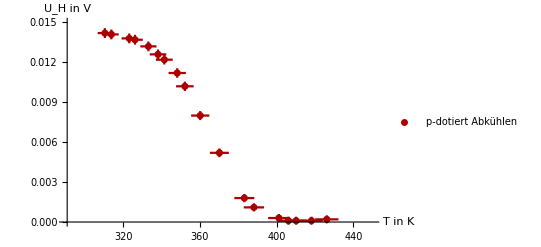

```mathematica
errPlotM33pA=ErrorListPlot[plotValuesM33pA,AxesLabel->{"T in K","U_H in  V"},PlotRange->{{290,450},{0,.015}},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert Abkühlen"},{.75,.75}]]
```

## Ergebnis M3.3

### Vergleich n- und p-dotiert

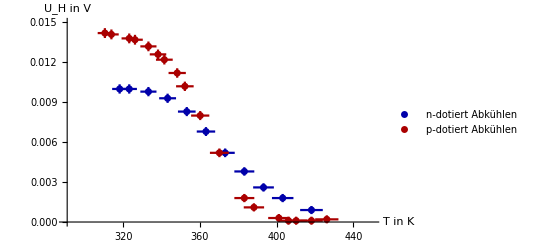

```mathematica
Show[errPlotM33nA,errPlotM33pA]
```

```mathematica
Show[errPlotM33nG,errPlotM33pG]
```

-Graphics-

### p-dotiert Springt wieder hoch!?!

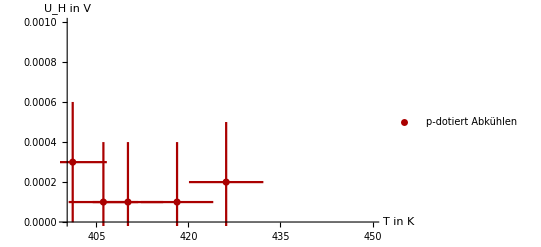

```mathematica
errPlotM33pAZoom=ErrorListPlot[plotValuesM33pA,AxesLabel->{"T in K","U_H in  V"},PlotRange->{{400,450},{0,.001}},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert Abkühlen"},{.75,.75}]]
```

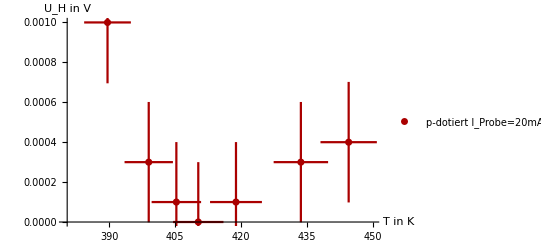

```mathematica
errPlotM33pGZoom=ErrorListPlot[plotValuesM33pG,AxesLabel->{"T in K","U_H in  V"},PlotRange->{{380,450},{0,.001}},PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert I_Probe=20mA"},{.75,.75}]]
```

### Vergleich Abkühlen und Gleichgewicht

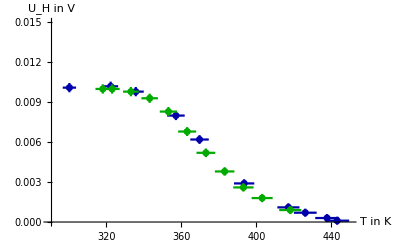

```mathematica
Show[errPlotM33nG,errPlotM33nA/._?ColorQ->Darker[Green]]
```

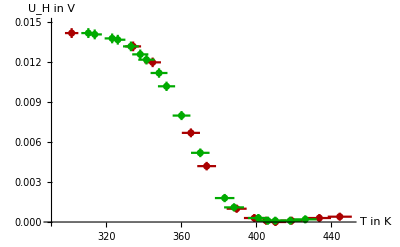

```mathematica
Show[errPlotM33pG,errPlotM33pA/._?ColorQ->Darker[Green]]
```